# ZSlice Solver

P Zimmerman and P Bourg

- Solves the upper triangular corrector tensor hierarchy for the NP components in {ω,m} modes using a “z-slice” algorithm which solves the r-transport equations at a given z=const from zmin=-1 to zmax =1 
- Uses reduced differential operators with pole safe rescaling
- Reads in the boundary data and effective source from binary

dependency chains 
-Graphics-

## Configurations (from Patrick)

##### Keyboard shortcuts

The following allows to auto-replace stuff when you write “tex[” into “TeXForm[StandardForm[]]”,
	which is what is needed to  output LATEX code of an equation. The StandardForm is needed if using the notation package.

```mathematica
CurrentValue[EvaluationNotebook[],{InputAutoReplacements,"tex"}]:=
	RowBox[{"TeXForm","[",RowBox[{"StandardForm","","]"}],"]"}]
```

##### Palettes and docked buttons

Below is the full docked buttons code. In the following sections, we explain each part.

Correctly re-enable evaluation property

This part of the above code creates a docked button that easily allows to deactivate cell evaluation and re - enable it,
	while keeping the texts, outputs,etc default (not evaluable).  Specifically, “re-enable” in fact just sets properties back to default.

```mathematica
buttonevaluable = ToBoxes@Column[Button[StringForm["Evaluable -> ``",#], 
CurrentValue[SelectedCells@InputNotebook[],Evaluatable]=#]&/@{False,Inherited}];
```

The below code does the same thing, but it creates a palette instead. Kept it for archive purposes.

```mathematica
(*CreatePalette@Column[Button[StringForm["Evaluatable -> ``",#],
	CurrentValue[SelectedCells@InputNotebook[],Evaluatable]=#]&/@{False,Inherited}]*)
```

Full docked buttons

Implementation of each part as a docked cell. For adding new features, simply create new data as shown for the above two buttons, i.e. ToBoxes[stuff] and then put it inside the BoxData.
				The next lines shoul not be touched and their purpose is to make the toolbar expand/collapse upon clicking of the bottom panel.

```mathematica
fullDockedCellsWithCollapseToolbar=Cell[BoxData[{buttonalignment,buttonevaluable}], 
					CellFrameLabelMargins->0,CellFrameLabels->{{None,None},{ButtonBox["",
				ButtonFunction:>Function[With[{pc=ParentCell@EvaluationCell[]},SetOptions[pc,If[CurrentValue[pc,CellSize]===0,{CellSize->Inherited,CellElementSpacings->{},
				CellFrameMargins->Inherited},{CellSize->0,CellElementSpacings->{"CellMinHeight"->0},CellFrameMargins->0}]]]], ImageSize->{Scaled[2],15},Evaluator->Automatic],None}}];
				SetOptions[EvaluationNotebook[],DockedCells->fullDockedCellsWithCollapseToolbar]
				Clear[buttonalignment,buttonevaluable]
```

## Generate Grid

```mathematica
rGrid=N@Subdivide[8,12,120];
zGrid=N@Subdivide[-9/10,9/10,20];
```

## Read the input source data

A couple of useful conventions are built in:
- it interprets X = (r-rp)/B,
- it interprets Y = -rp z,
- if YStorage -> “HalfWithEvenReflection”, it evaluates using Abs[Y],
- if m<0 and the metadata says NegativeMIsConjugate -> True, it loads |m| and returns the conjugate.

### Worldtube data

### Reader Helper

```mathematica
ClearAll[readSourceBulkBinaryFile];
ClearAll[$GHZSrcMagicBytes,decodeSourceFlags];

$GHZSrcMagicBytes=Join[ToCharacterCode["GHZSRC1"],{0}];

decodeSourceFlags[flags_Integer]:=<|"RawFlags"->flags,"NegativeMIsConjugate"->BitAnd[flags,1]=!=0|>;
ClearAll[readSourceBulkBinaryFile];

readSourceBulkBinaryFile[file_String]:=Module[{stream,magic,version,m,componentID,patchID,yStorageID,flags,flagInfo,rp,B,nx,ny,xGrid,yGrid,flat,data},stream=OpenRead[file,BinaryFormat->True];
If[stream===$Failed,Return[$Failed]];
magic=BinaryReadList[stream,"Byte",8];
version=BinaryRead[stream,"UnsignedInteger32"];
m=BinaryRead[stream,"Integer32"];
componentID=BinaryRead[stream,"UnsignedInteger32"];
patchID=BinaryRead[stream,"UnsignedInteger32"];
yStorageID=BinaryRead[stream,"UnsignedInteger32"];
flags=BinaryRead[stream,"UnsignedInteger32"];
rp=BinaryRead[stream,"Real64"];
B=BinaryRead[stream,"Real64"];
nx=BinaryRead[stream,"UnsignedInteger64"];
ny=BinaryRead[stream,"UnsignedInteger64"];
xGrid=BinaryReadList[stream,"Real64",nx];
yGrid=BinaryReadList[stream,"Real64",ny];
flat=BinaryReadList[stream,"Real64",2 nx ny];
Close[stream];
If[magic=!=$GHZSrcMagicBytes,Print["readSourceBulkBinaryFile: bad magic bytes in ",file];
Return[$Failed];];
data=Partition[Map[Complex@@#&,Partition[flat,2]],ny];
flagInfo=decodeSourceFlags[flags];
<|"Magic"->magic,"Version"->version,"m"->m,"ComponentID"->componentID,"PatchID"->patchID,"YStorageID"->yStorageID,"Flags"->flags,"NegativeMIsConjugate"->flagInfo["NegativeMIsConjugate"],"rp"->rp,"B"->B,"nx"->nx,"ny"->ny,"XGrid"->xGrid,"YGrid"->yGrid,"Data"->data|>]
buildComponentMatrix[fun_,m_,XGrid_List,YGrid_List]:=Table[fun[m][x,y],{x,XGrid},{y,YGrid}];
```

### Sampler Helper

```mathematica
ClearAll[makeBulkSourceSampler];

makeBulkSourceSampler[src_Association,order_:3]:=Module[{xGrid,yGrid,data,reIF,imIF,yStorageID,rp,B,xMin,xMax,yMin,yMax},xGrid=src["XGrid"];
yGrid=src["YGrid"];
data=src["Data"];
yStorageID=src["YStorageID"];
rp=src["rp"];
B=src["B"];
xMin=Min[xGrid];xMax=Max[xGrid];
yMin=Min[yGrid];yMax=Max[yGrid];
reIF=ListInterpolation[Re[data],{xGrid,yGrid},InterpolationOrder->order];
imIF=ListInterpolation[Im[data],{xGrid,yGrid},InterpolationOrder->order];
<|"SampleXY"->Function[{x,y},Module[{xx,yy},yy=If[yStorageID==1,Abs[y],y];
xx=Clip[x,{xMin,xMax}];
yy=Clip[yy,{yMin,yMax}];
reIF[xx,yy]+I imIF[xx,yy]]],"SamplePhysical"->Function[{r,z},Module[{x,y,xx,yy},x=(r-rp)/B;
y=-rp z;
yy=If[yStorageID==1,Abs[y],y];
xx=Clip[x,{xMin,xMax}];
yy=Clip[yy,{yMin,yMax}];
reIF[xx,yy]+I imIF[xx,yy]]]|>]
```

## boundary data

### Reader

```mathematica
ClearAll[$GHZBdyComponentNamesByID,$GHZBdyKindNamesByID,$GHZBdyYStorageNamesByID,$GHZBdyMagicBytes,$GHZBdyFlagBits,decodeBoundaryFlags,readBoundaryBinaryFile,makeBoundarySampler];

$GHZBdyComponentNamesByID=<|0->"ll",1->"ln",2->"lm",3->"lmb"|>;
$GHZBdyKindNamesByID=<|0->"delta",1->"deltaPrime"|>;
$GHZBdyYStorageNamesByID=<|0->"Full",1->"HalfWithEvenReflection"|>;

$GHZBdyMagicBytes=Join[ToCharacterCode["GHZBND1"],{0}];

$GHZBdyFlagBits=<|"NegativeMIsConjugate"->1,"MostlyPlusSignature"->2|>;

decodeBoundaryFlags[flags_Integer]:=<|"RawFlags"->flags,"NegativeMIsConjugate"->BitAnd[flags,$GHZBdyFlagBits["NegativeMIsConjugate"]]=!=0,"MetricSignature"->If[BitAnd[flags,$GHZBdyFlagBits["MostlyPlusSignature"]]=!=0,"MostlyPlus","MostlyMinus"]|>;

readBoundaryBinaryFile[file_String]:=Module[{stream,magic,version,m,componentID,kindID,yStorageID,flags,flagInfo,rp,rBoundary,ny,yGrid,flat,data},stream=OpenRead[file,BinaryFormat->True];
If[stream===$Failed,Return[$Failed]];
magic=BinaryReadList[stream,"Byte",Length[$GHZBdyMagicBytes]];
version=BinaryRead[stream,"UnsignedInteger32"];
m=BinaryRead[stream,"Integer32"];
componentID=BinaryRead[stream,"UnsignedInteger32"];
kindID=BinaryRead[stream,"UnsignedInteger32"];
yStorageID=BinaryRead[stream,"UnsignedInteger32"];
flags=BinaryRead[stream,"UnsignedInteger32"];
rp=BinaryRead[stream,"Real64"];
rBoundary=BinaryRead[stream,"Real64"];
ny=BinaryRead[stream,"UnsignedInteger64"];
yGrid=BinaryReadList[stream,"Real64",ny];
flat=BinaryReadList[stream,"Real64",2 ny];
Close[stream];
If[magic=!=$GHZBdyMagicBytes,Print["readBoundaryBinaryFile: bad magic bytes in ",file];
	Return[$Failed];];
data=Map[Complex@@#&,Partition[flat,2]];
flagInfo=decodeBoundaryFlags[flags];
<|
"File"->file,
"Magic"->magic,
"Version"->version,
"m"->m,
"ComponentID"->componentID,
"Component"->Lookup[$GHZBdyComponentNamesByID,componentID,Missing["UnknownComponentID",componentID]],
"KindID"->kindID,
"Kind"->Lookup[$GHZBdyKindNamesByID,kindID,Missing["UnknownKindID",kindID]],
"YStorageID"->yStorageID,"YStorage"->Lookup[$GHZBdyYStorageNamesByID,yStorageID,Missing["UnknownYStorageID",yStorageID]],
"Flags"->flags,
"NegativeMIsConjugate"->flagInfo["NegativeMIsConjugate"],
"MetricSignature"->flagInfo["MetricSignature"],
"rp"->rp,
"rBoundary"->rBoundary,
"ny"->ny,
"YGrid"->yGrid,
"Data"->data
|>]
```

### Sampler

```mathematica
ClearAll[makeBoundarySampler];

makeBoundarySampler[src_Association,order_:1]:=Module[{yGrid,data,reIF,imIF,yStorageID,rp,rBoundary,yMin,yMax},yGrid=src["YGrid"];
data=src["Data"];
yStorageID=src["YStorageID"];
rp=src["rp"];
rBoundary=src["rBoundary"];
yMin=Min[yGrid];yMax=Max[yGrid];
reIF=ListInterpolation[{Re[data]},{{1},yGrid},InterpolationOrder->{0,order}];
imIF=ListInterpolation[{Im[data]},{{1},yGrid},InterpolationOrder->{0,order}];
<|"rBoundary"->rBoundary,"SampleY"->Function[{y},Module[{yy},yy=If[yStorageID==1,Abs[y],y];
yy=Clip[yy,{yMin,yMax}];
reIF[1,yy]+I imIF[1,yy]]],"Samplez"->Function[{z},Module[{y,yy},y=-rp z;
yy=If[yStorageID==1,Abs[y],y];
yy=Clip[yy,{yMin,yMax}];
reIF[1,yy]+I imIF[1,yy]]]|>]
```

```mathematica
ClearAll[makeBoundaryModeSamplers];

Options[makeBoundaryModeSamplers]={"StoredCoordinate"->"Y"};
makeBoundaryModeSamplers[bdyData_Association,order_:1,___]:=Association@KeyValueMap[(#1->makeBoundarySampler[#2,order])&,bdyData];
```

## Mode loader

```mathematica
ClearAll[$GHZBdyComponents,$GHZBdyKinds,readBoundaryModeData,makeBoundaryModeSamplers,bdyVal];

$GHZBdyComponents={"ll","ln","lm","lmb"};
$GHZBdyKinds={"delta","deltaPrime"};

readBoundaryModeData[dir_String,m_Integer,prefix_:"TeffBdy"]:=Association@Flatten@Table[({comp,kind}->readBoundaryBinaryFile[FileNameJoin[{dir,StringTemplate["``_``_``_m``.bin"][prefix,comp,kind,Abs[m]]}]]),{comp,$GHZBdyComponents},{kind,$GHZBdyKinds}];

makeBoundaryModeSamplers[bdyData_Association,order_:1]:=AssociationMap[makeBoundarySampler[bdyData[#],order]&,Keys[bdyData]];

bdyVal[bdySamplers_Association,comp_String,kind_String,z_?NumericQ]:=bdySamplers[{comp,kind}]["Samplez"][z];
```

```mathematica
makeSourceFieldFromExpr[expr_,rGrid_List,zGrid_List,meta_:<||>]:=Module[{f,vals},f=Function[{rr,zz},Evaluate[N[expr/. {r->rr,z->zz}]]];
vals=Table[f[rr,zz],{rr,rGrid},{zz,zGrid}];
<|"Meta"->Join[<|"RGrid"->N@rGrid,"ZGrid"->N@zGrid|>,meta],"Data"->vals|>]
```

#### pieces of the stress tensor we need to differentiate

```mathematica
ClearAll[makeBoundaryProfiles];

makeBoundaryProfiles[corrData_Association]:=<|"TllDelta"->Function[{z},corrData["BoundaryValue"]["ll","delta",z]],"TllDeltaPrime"->Function[{z},corrData["BoundaryValue"]["ll","deltaPrime",z]],"TlmDelta"->Function[{z},corrData["BoundaryValue"]["lm","delta",z]],"TlmDeltaPrime"->Function[{z},corrData["BoundaryValue"]["lm","deltaPrime",z]],"TlmbDeltaPrime"->Function[{z},corrData["BoundaryValue"]["lmb","deltaPrime",z]],"TlnDelta"->Function[{z},corrData["BoundaryValue"]["ln","delta",z]],"TlnDeltaPrime"->Function[{z},corrData["BoundaryValue"]["ln","deltaPrime",z]]|>;
```

```mathematica
ClearAll[makeBoundaryDerivativeProfiles];

makeBoundaryDerivativeProfiles[profiles_Association,m_Integer,omegaMK_,ethBuilder_,ethBarBuilder_,sTll_Integer,sTlm_Integer,sTlmb_Integer]:=Module[{ethTll,ethTlmb,ethbarTlm},ethTll=ethBuilder[profiles["TllDeltaPrime"],m,omegaMK,sTll];
ethTlmb=ethBuilder[profiles["TlmbDeltaPrime"],m,omegaMK,sTlmb];
ethbarTlm=ethBarBuilder[profiles["TlmDeltaPrime"],m,omegaMK,sTlm];
<|"pduTllDeltaPrime"->Function[{z},-I omegaMK profiles["TllDeltaPrime"][z]],"ethTllDeltaPrime"->ethTll,
"ethTlmbDeltaPrime"->ethTlmb,
"ethbarTlmDeltaPrime"->ethbarTlm|>];
```

#### Held ops on modes for the boundary data

```mathematica
(* derivatives we need for the initial data *)
ClearAll[heldEthOnMode,heldEthBarOnMode];
heldEthOnMode[profile_,m_Integer,omega_,s_Integer,ethBuilder_]:=ethBuilder[profile,m,omega,s];
heldEthBarOnMode[profile_,m_Integer,omega_,s_Integer,ethBarBuilder_]:=ethBarBuilder[profile,m,omega,s];
```

## Corrector mode assembly

```mathematica
ClearAll[$GHZSrcComponents,readSourcePatchData];

$GHZSrcComponents={"ll","ln","lm","lmb","nn","nm","nmb","mm","mmb"};
```

### Mode sampler assembly

```mathematica
ClearAll[makeBoundaryModeSamplers, makePatchComponentSamplers];
```

```mathematica
makeBoundaryModeSamplers[bdyData_Association,order_:1,___]:=Association@KeyValueMap[(#1->makeBoundarySampler[#2,order])&,bdyData]
```

```mathematica
makePatchComponentSamplers[patchData_Association,order_:1,___]:=Association@KeyValueMap[(#1->makeBulkSourceSampler[#2,order])&,patchData];
```

### main loader

```mathematica
ClearAll[readWorldtubeModeData];

readWorldtubeModeData[dir_String,m_Integer,prefix_:"Teff"]:=Module[{mStored=Abs[m]},<|"Left"->readSourcePatchData[dir,mStored,"left",prefix],"Right"->readSourcePatchData[dir,mStored,"right",prefix]|>];
```

```mathematica
readSourcePatchData[dir_String,m_Integer,patch_String,prefix_:"Teff"]:=Module[{mStored=Abs[m]},If[!MemberQ[{"left","right"},patch],Print["readSourcePatchData: patch must be \"left\" or \"right\"."];
Return[$Failed];];
AssociationMap[readSourceBulkBinaryFile[FileNameJoin[{dir,StringTemplate["``_``_m``_``.bin"][prefix,#,mStored,patch]}]]&,$GHZSrcComponents]];


(*makePatchComponentSamplers[patchData_Association,order_:1]:=AssociationMap[makeBulkSourceSampler[patchData[#],order]&,Keys[patchData]];*)

Options[loadCorrectorData]={"BulkPrefix"->"Teff","BoundaryPrefix"->"TeffBdy","BulkInterpolationOrder"->1,"BoundaryInterpolationOrder"->1,"AtParticleAction"->"Average","BoundaryStoredCoordinate"->"Y"};

loadCorrectorData[m_Integer,bulkDir_String,bdyDir_String,OptionsPattern[]]:=Module[{mStored=Abs[m],bulkData,boundaryData,bulkSamplersLeft,bulkSamplersRight,boundarySamplers,bulkLeftMeta,bulkRightMeta,bdyMeta,rp,B,rBoundary,negBulkQ,negBdyQ,negQ,conjWrap,sampleBoundary,sampleBulk,atParticleAction},atParticleAction=OptionValue["AtParticleAction"];
bulkData=readWorldtubeModeData[bulkDir,mStored,OptionValue["BulkPrefix"]];
boundaryData=readBoundaryModeData[bdyDir,mStored,OptionValue["BoundaryPrefix"]];
bulkSamplersLeft=makePatchComponentSamplers[bulkData["Left"],OptionValue["BulkInterpolationOrder"]];
bulkSamplersRight=makePatchComponentSamplers[bulkData["Right"],OptionValue["BulkInterpolationOrder"]];
boundarySamplers=makeBoundaryModeSamplers[boundaryData,OptionValue["BoundaryInterpolationOrder"],"StoredCoordinate"->OptionValue["BoundaryStoredCoordinate"]];
bulkLeftMeta=First[Values[bulkData["Left"]]];
bulkRightMeta=First[Values[bulkData["Right"]]];
bdyMeta=First[Values[boundaryData]];
rp=bulkLeftMeta["rp"];
B=bulkLeftMeta["B"];
rBoundary=bdyMeta["rBoundary"];
negBulkQ=TrueQ[bulkLeftMeta["NegativeMIsConjugate"]]&&TrueQ[bulkRightMeta["NegativeMIsConjugate"]];
negBdyQ=TrueQ[bdyMeta["NegativeMIsConjugate"]];
negQ=negBulkQ&&negBdyQ;
conjWrap=If[m<0&&negQ,Conjugate[#]&,Identity];
sampleBoundary=Function[{comp,kind,z},conjWrap[boundarySamplers[{comp,kind}]["Samplez"][z]]];
sampleBulk=Function[{comp,r,z},Module[{x,val},x=(r-rp)/B;
val=Which[x<0,bulkSamplersLeft[comp]["SamplePhysical"][r,z],x>0,bulkSamplersRight[comp]["SamplePhysical"][r,z],True,Switch[atParticleAction,"Left",bulkSamplersLeft[comp]["SamplePhysical"][r,z],"Right",bulkSamplersRight[comp]["SamplePhysical"][r,z],_,(bulkSamplersLeft[comp]["SamplePhysical"][r,z]+bulkSamplersRight[comp]["SamplePhysical"][r,z])/2]];
conjWrap[val]]];
<|"RequestedMode"->m,"StoredMode"->mStored,"Meta"-><|"rp"->rp,"B"->B,"rBoundary"->rBoundary,"NegativeMIsConjugate"->negQ,"MetricSignature"->bdyMeta["MetricSignature"]|>,"BulkLeft"->bulkData["Left"],"BulkRight"->bulkData["Right"],"BulkSamplersLeft"->bulkSamplersLeft,"BulkSamplersRight"->bulkSamplersRight,"BoundaryData"->boundaryData,"BoundarySamplers"->boundarySamplers,"BulkValue"->sampleBulk,"BoundaryValue"->sampleBoundary|>]
```

### left-boundary X(rmin) data

#### Xmmbar

```mathematica
(*ClearAll[makeInitDataXmmbar];


makeInitDataXmmbar[corrData_Association,bgFun_]:=Function[{z0},Module[{bg,TllDelta,TllDeltaPrime,y0,yp0},bg=bgFun[z0];
TllDelta=corrData["BoundaryValue"]["ll","delta",z0];
TllDeltaPrime=corrData["BoundaryValue"]["ll","deltaPrime",z0];
y0=TllDeltaPrime;
yp0=TllDelta+(bg["rho"]+bg["rhob"]) TllDeltaPrime;
{y0,yp0}]];

(*makeInitDataXmmbar[bdySamplers_Association,bgFun_]:=Function[{z0},Module[{
bg,
TllDelta,TllDeltaPrime,
y0,yp0},
bg=bgFun[z0]; (*eg with bgFun=MakeBoundaryBGFun[bg,rmin] below *)
TllDelta=bdyVal[bdySamplers,"ll","delta",z0];
TllDeltaPrime=bdyVal[bdySamplers,"ll","deltaPrime",z0];
y0=TllDeltaPrime;
yp0=TllDelta+(bg["rho"]+bg["rhob"]) TllDeltaPrime;
{y0,yp0}]];*)*)
```

```mathematica
(* ========================================= *)
(* ---- Xmmbar boundary / initial data ------ *)
(* ========================================= *)
ClearAll[makeInitDataXmmbar];makeInitDataXmmbar[corrData_Association,bgFun_]:=Function[{z0},Module[{zz,bg,TllDelta,TllDeltaPrime,y0,yp0},zz=N[z0];bg=bgFun[zz];TllDelta=N@corrData["BoundaryValue"]["ll","delta",zz];TllDeltaPrime=N@corrData["BoundaryValue"]["ll","deltaPrime",zz];y0=TllDeltaPrime;yp0=TllDelta+(bg["rho"]+bg["rhob"]) TllDeltaPrime;N[{y0,yp0}]]];
```

```mathematica
bdyDir="/Users/antares/Projects/physics_codes/GHZ_numeric/Data/TeffBoundaryBinary";
```

```mathematica
bdyTest=readBoundaryBinaryFile["/Users/antares/Projects/physics_codes/GHZ_numeric/Data/TeffBoundaryBinary/TeffBdy_ll_delta_m0.bin"];
MinMax[bdyTest["YGrid"]]
bdyTest["rp"]
```

{0.,10.}

10.

#### X_nm

```mathematica
ClearAll[makeInitDataXnm];
makeInitDataXnm[corrData_Association, bgFun_, ethTllDeltaPrimeFun_] :=
  Function[{z0},
    Module[{bg, TlmDelta, TlmDeltaPrime, ethTllDeltaPrime, y0, yp0},
      bg = bgFun[z0];

      TlmDelta = corrData["BoundaryValue"]["lm", "delta", z0];
      TlmDeltaPrime = corrData["BoundaryValue"]["lm", "deltaPrime", z0];
      ethTllDeltaPrime = ethTllDeltaPrimeFun[z0];

      y0 = 2 TlmDeltaPrime;
      yp0 = 4 bg["rho"] TlmDeltaPrime + 2 TlmDelta - bg["rho"] ethTllDeltaPrime;

      {y0, yp0}
    ]
  ];
```

#### X_nn

```mathematica
ClearAll[makeInitDataXnn];

makeInitDataXnn[corrData_Association,bgFun_,duTllDeltaPrimeFun_,ethTlmbDeltaPrimeFun_,ethbarTlmDeltaPrimeFun_]:=Function[{z0},Module[{bg,TlnDelta,TllDelta,TllDeltaPrime,TlmDeltaPrime,TlmbDeltaPrime,duTllDeltaPrime,ethTlmbDeltaPrime,ethbarTlmDeltaPrime,numer,denom},bg=bgFun[z0];
TlnDelta=corrData["BoundaryValue"]["ln","delta",z0];
TllDelta=corrData["BoundaryValue"]["ll","delta",z0];
TllDeltaPrime=corrData["BoundaryValue"]["ll","deltaPrime",z0];
TlmDeltaPrime=corrData["BoundaryValue"]["lm","deltaPrime",z0];
TlmbDeltaPrime=corrData["BoundaryValue"]["lmb","deltaPrime",z0];
duTllDeltaPrime=duTllDeltaPrimeFun[z0];
ethTlmbDeltaPrime=ethTlmbDeltaPrimeFun[z0];
ethbarTlmDeltaPrime=ethbarTlmDeltaPrimeFun[z0];
numer=TlnDelta-(bg["Delta"]/(2 bg["Sigma"])) TllDelta+((bg["r"]^2+bg["a"]^2)/bg["Sigma"]) duTllDeltaPrime-(bg["r"] bg["Delta"]/bg["Sigma"]^2) TllDeltaPrime-(bg["rho"] ethTlmbDeltaPrime+bg["rhob"] ethbarTlmDeltaPrime)+2 bg["rho"] bg["rhob"] (bg["tau0"] TlmbDeltaPrime+bg["taub0"] TlmDeltaPrime);
denom=(1/2) (bg["rho"]+bg["rhob"]);
numer/denom]];
```

## Operators and Bkgd

## Background Fields

```mathematica
(* =========================================*)
(*----------background scalars ----------*)
(* =========================================*)
ClearAll[RhoBG,RhobBG,TauHBG,TauHBarBG,RhopHBG,PsiHBG,OmHBG];

RhoBG[bg_,r_,z_]:=-1/(r-I bg["a"] z);
RhobBG[bg_,r_,z_]:=-1/(r+I bg["a"] z);

TauHBG[bg_,z_]:=-(I bg["a"]/Sqrt[2]) Sqrt[1-z^2];
TauHBarBG[bg_,z_]:=(I bg["a"]/Sqrt[2]) Sqrt[1-z^2];
RhopHBG[bg_,z_]:=-1/2;
PsiHBG[bg_,z_]:=bg["M"];
OmHBG[bg_,z_]:=-2 I bg["a"] z;

ClearAll[MakeBackground,SigmaBG,DeltaBG,RhoBG,RhobBG,TauHBG,TauHBarBG,RhopHBG,PsiHBG,OmHBG];

MakeBackground[pars_Association]:=<|"a"->N@pars["a"],"M"->N@pars["M"],"Q"->N@Lookup[pars,"Q",0]|>;

SigmaBG[bg_Association,rr_,zz_]:=rr^2+bg["a"]^2 zz^2;
DeltaBG[bg_Association,rr_]:=rr^2-2 bg["M"] rr+bg["a"]^2+bg["Q"]^2;

RhoBG[bg_Association,rr_,zz_]:=-1/(rr-I bg["a"] zz);
RhobBG[bg_Association,rr_,zz_]:=-1/(rr+I bg["a"] zz);

TauHBG[bg_Association,zz_]:=-(I bg["a"]/Sqrt[2]) Sqrt[1-zz^2];
TauHBarBG[bg_Association,zz_]:=(I bg["a"]/Sqrt[2]) Sqrt[1-zz^2];
RhopHBG[bg_Association,zz_]:=-1/2;
PsiHBG[bg_Association,zz_]:=bg["M"];
OmHBG[bg_Association,zz_]:=-2 I bg["a"] zz;
```

```mathematica
(* =========== background helper func ===============*)
```

```mathematica
ClearAll[MakeBoundaryBGFun];

MakeBoundaryBGFun[bg_Association,rBoundary_?NumericQ]:=Function[{z0},<|"r"->N[rBoundary],"a"->N[bg["a"]],"M"->N[bg["M"]],"Q"->N[bg["Q"]],"rho"->N@RhoBG[bg,rBoundary,z0],"rhob"->N@RhobBG[bg,rBoundary,z0],"Delta"->N@DeltaBG[bg,rBoundary],"Sigma"->N@SigmaBG[bg,rBoundary,z0],"tau0"->N@TauHBG[bg,z0],"taub0"->N@TauHBarBG[bg,z0],"rhop0"->N@RhopHBG[bg,z0],"psi0"->N@PsiHBG[bg,z0],"om0"->N@OmHBG[bg,z0]|>];
```

## Operators

### Held ops (raw and reduced)

```mathematica
(*Reduced Held Operators*)
(*Pole-factorized Held operators in outgoing Kerr coordinates*)

(*----------assumptions----------*)
$Assumptions=Element[{m,s},Integers]&&Element[{a,M,r,z,ω},Reals]&&-1<z<1;

(*----------Kerr background in outgoing coordinates----------*)
Δ[r_]:=r^2-2 M r+a^2;
Σ[r_,z_]:=r^2+a^2 z^2;

Sfac[z_]:=Sqrt[1-z^2];

(*----------pole factor----------*)
alpha[m_,s_]:=Abs[m+s]/2;
beta[m_,s_]:=Abs[m-s]/2;

W[m_,s_][z_]:=(1-z)^alpha[m,s] (1+z)^beta[m,s];

(*----------spin from GHP weights,if you want to use p,q----------*)
spinFromPQ[p_,q_]:=(p-q)/2;

(*----------raw Held operators acting on an expression expr[r,z]----------*)
(*These match  current C++ edth_core_RSlice_with_extrapolation conventions.*)

EthHRaw[m_,s_,ω_][expr_]:=1/Sqrt[2]*(Sfac[z] D[expr,z]+((m+s z)/Sfac[z]-a ω Sfac[z]) expr);

EthBarHRaw[m_,s_,ω_][expr_]:=1/Sqrt[2]*(Sfac[z] D[expr,z]-((m+s z)/Sfac[z]-a ω Sfac[z]) expr);

(*Held thorn operators in outgoing Kerr coordinates*)
ThornRaw[expr_]:=D[expr,r];

ThornPHRaw[ω_][expr_]:=-I ω expr;

ThornPHrRaw[ω_][expr_]:=-I ω expr-(Δ[r]/(2 Σ[r,z])) D[expr,r];

(*----------reduced fields----------*)
(*F_s(r,z)=W_{m,s}(z) G_s(r,z)*)

(*Reduced first-order operators:
\hat{eth}_s=W_{m,s+1}^{-1} eth_H W_{m,s}\hat{ethbar}_s=W_{m,s-1}^{-1} ethBar_H W_{m,s}*)

EthHRed[m_,s_,ω_][gexpr_]:=Assuming[$Assumptions,FullSimplify[Cancel[EthHRaw[m,s,ω][W[m,s][z] gexpr]/W[m,s+1][z]]]];

EthBarHRed[m_,s_,ω_][gexpr_]:=Assuming[$Assumptions,FullSimplify[Cancel[EthBarHRaw[m,s,ω][W[m,s][z] gexpr]/W[m,s-1][z]]]];

(*Reduced radial Held operators:W depends only on z,so these are unchanged*)
ThornRed[m_,s_][gexpr_]:=Assuming[$Assumptions,FullSimplify[Cancel[ThornRaw[W[m,s][z] gexpr]/W[m,s][z]]]];

ThornPHRed[m_,s_,ω_][gexpr_]:=Assuming[$Assumptions,FullSimplify[Cancel[ThornPHRaw[ω][W[m,s][z] gexpr]/W[m,s][z]]]];

ThornPHrRed[m_,s_,ω_][gexpr_]:=Assuming[$Assumptions,FullSimplify[Cancel[ThornPHrRaw[ω][W[m,s][z] gexpr]/W[m,s][z]]]];

(*----------direct reduced compositions----------*)
(*These avoid forming a raw intermediate field numerically.*)

EthHEthBarHRed[m_,s_,ω_][gexpr_]:=Assuming[$Assumptions,FullSimplify[Cancel[EthHRaw[m,s-1,ω][EthBarHRaw[m,s,ω][W[m,s][z] gexpr]]/W[m,s][z]]]];

EthBarHEthHRed[m_,s_,ω_][gexpr_]:=Assuming[$Assumptions,FullSimplify[Cancel[EthBarHRaw[m,s+1,ω][EthHRaw[m,s,ω][W[m,s][z] gexpr]]/W[m,s][z]]]];

CommutatorEthsRed[m_,s_,ω_][gexpr_]:=Assuming[$Assumptions,FullSimplify[EthHEthBarHRed[m,s,ω][gexpr]-EthBarHEthHRed[m,s,ω][gexpr]]];

(*----------helpers for pretty output----------*)

ClearAll[CollectDerivs];
CollectDerivs[expr_,g_Symbol]:=Collect[Expand[Together[expr]],{g[r,z],Derivative[1,0][g][r,z],Derivative[0,1][g][r,z],Derivative[2,0][g][r,z],Derivative[1,1][g][r,z],Derivative[0,2][g][r,z]},FullSimplify];

ClearAll[ShowReducedOperators];
ShowReducedOperators[m0_Integer,s0_Integer,g_Symbol:G]:=<|"W_s"->FullSimplify[W[m0,s0][z]],"W_s+1"->FullSimplify[W[m0,s0+1][z]],"W_s-1"->FullSimplify[W[m0,s0-1][z]],"EthHRed"->CollectDerivs[PiecewiseExpand@FunctionExpand@EthHRed[m0,s0,ω][g[r,z]],g],"EthBarHRed"->CollectDerivs[PiecewiseExpand@FunctionExpand@EthBarHRed[m0,s0,ω][g[r,z]],g],"ThornRed"->CollectDerivs[PiecewiseExpand@FunctionExpand@ThornRed[m0,s0][g[r,z]],g],"ThornPHRed"->CollectDerivs[PiecewiseExpand@FunctionExpand@ThornPHRed[m0,s0,ω][g[r,z]],g],"ThornPHrRed"->CollectDerivs[PiecewiseExpand@FunctionExpand@ThornPHrRed[m0,s0,ω][g[r,z]],g],"EthHEthBarHRed"->CollectDerivs[PiecewiseExpand@FunctionExpand@EthHEthBarHRed[m0,s0,ω][g[r,z]],g],"EthBarHEthHRed"->CollectDerivs[PiecewiseExpand@FunctionExpand@EthBarHEthHRed[m0,s0,ω][g[r,z]],g],"Commutator"->CollectDerivs[PiecewiseExpand@FunctionExpand@CommutatorEthsRed[m0,s0,ω][g[r,z]],g]|>;

(*----------optional p,q wrappers----------*)

EthHRedPQ[m_,p_,q_,ω_][gexpr_]:=EthHRed[m,spinFromPQ[p,q],ω][gexpr];

EthBarHRedPQ[m_,p_,q_,ω_][gexpr_]:=EthBarHRed[m,spinFromPQ[p,q],ω][gexpr];

EthHEthBarHRedPQ[m_,p_,q_,ω_][gexpr_]:=EthHEthBarHRed[m,spinFromPQ[p,q],ω][gexpr];

EthBarHEthHRedPQ[m_,p_,q_,ω_][gexpr_]:=EthBarHEthHRed[m,spinFromPQ[p,q],ω][gexpr];
```

## Held Fields

### Raw

```mathematica
(*----------raw Held fields----------*)ClearAll[MakeHeldField,HeldExpr,HeldType,HeldSpin,HeldMode,ShiftHeldType];

MakeHeldField[expr_,{p_Integer,q_Integer},{ω_,m_Integer}]:=<|"Expr"->expr,"Type"-><|"p"->p,"q"->q,"s"->(p-q)/2|>,"Mode"-><|"ω"->ω,"m"->m|>|>;

HeldExpr[field_Association]:=field["Expr"];
HeldType[field_Association]:=field["Type"];
HeldSpin[field_Association]:=field["Type"]["s"];
HeldMode[field_Association]:=field["Mode"];

ShiftHeldType[field_Association,{dp_Integer,dq_Integer},expr_]:=MakeHeldField[expr,{HeldType[field]["p"]+dp,HeldType[field]["q"]+dq},{HeldMode[field]["ω"],HeldMode[field]["m"]}];

(*----------raw Held operators----------*)

ClearAll[HeldP,HeldPp,HeldEth,HeldEthBar];

HeldP[field_Association]:=ShiftHeldType[field,{1,1},D[HeldExpr[field],r]];

HeldPp[field_Association,bg_Association]:=Module[{expr,ω},expr=HeldExpr[field];
ω=HeldMode[field]["ω"];
ShiftHeldType[field,{-1,-1},-I ω expr-(DeltaBG[bg,r]/(2 SigmaBG[bg,r,z])) D[expr,r]]];

HeldEth[field_Association,bg_Association]:=Module[{expr,ω,mm,ss,λ},expr=HeldExpr[field];
ω=HeldMode[field]["ω"];
mm=HeldMode[field]["m"];
ss=HeldSpin[field];
λ=Sqrt[1-z^2];
ShiftHeldType[field,{1,-1},(1/Sqrt[2]) (λ D[expr,z]-bg["a"] ω λ expr+((mm+ss z)/λ) expr)]];

HeldEthBar[field_Association,bg_Association]:=Module[{expr,ω,mm,ss,λ},expr=HeldExpr[field];
ω=HeldMode[field]["ω"];
mm=HeldMode[field]["m"];
ss=HeldSpin[field];
λ=Sqrt[1-z^2];
ShiftHeldType[field,{-1,1},(1/Sqrt[2]) (λ D[expr,z]+bg["a"] ω λ expr-((mm+ss z)/λ) expr)]];

ClearAll[BuildHeldDerivPack];

BuildHeldDerivPack[field_Association,bg_Association]:=<|"X"->field,"P_X"->HeldP[field],"Pp_X"->HeldPp[field,bg],"EH_X"->HeldEth[field,bg],"EbH_X"->HeldEthBar[field,bg],"EH_P_X"->HeldEth[HeldP[field],bg],"EbH_P_X"->HeldEthBar[HeldP[field],bg],"EbH_EH_X"->HeldEthBar[HeldEth[field,bg],bg],"PpHr_P_X"->HeldPp[HeldP[field],bg]|>;
```

### Reduced Held Fields

```mathematica
(* =========================================*)
(*----------reduced fields----------*)
(* =========================================*)ClearAll[MakeReducedField,RedExpr,RedSpin,RedMode,ModeOmega,ModeM,ShiftReducedSpin,RawExpr];

MakeReducedField[expr_,s_Integer,{ω_,m_Integer}]:=<|"Expr"->expr,"Spin"->s,"Mode"-><|"ω"->ω,"m"->m|>|>;

RedExpr[field_Association]:=field["Expr"];
RedSpin[field_Association]:=field["Spin"];
RedMode[field_Association]:=field["Mode"];
ModeOmega[field_Association]:=RedMode[field]["ω"];
ModeM[field_Association]:=RedMode[field]["m"];

ShiftReducedSpin[field_Association,ds_Integer,expr_]:=MakeReducedField[expr,RedSpin[field]+ds,{ModeOmega[field],ModeM[field]}];

RawExpr[field_Association]:=W[ModeM[field],RedSpin[field]][z] RedExpr[field];

(*substitute numeric bg parameters into symbolic reduced operators*)
ClearAll[InstantiateBG];
InstantiateBG[expr_,bg_Association]:=expr/. {a->bg["a"],M->bg["M"],Q->bg["Q"]};
(* =========================================*)
(*----------reduced Held operators----------*)
(* =========================================*)
ClearAll[HeldPRedField,HeldPpRedField,HeldEthRedField,HeldEthBarRedField,BuildReducedHeldDerivPack];

HeldPRedField[field_Association,bg_Association]:=Module[{mm,ss,ω,expr},mm=ModeM[field];ss=RedSpin[field];ω=ModeOmega[field];expr=RedExpr[field];
ShiftReducedSpin[field,0,InstantiateBG[ThornRed[mm,ss][expr],bg]]];

HeldPpRedField[field_Association,bg_Association]:=Module[{mm,ss,ω,expr},mm=ModeM[field];ss=RedSpin[field];ω=ModeOmega[field];expr=RedExpr[field];
ShiftReducedSpin[field,0,InstantiateBG[ThornPHrRed[mm,ss,ω][expr],bg]]];

HeldEthRedField[field_Association,bg_Association]:=Module[{mm,ss,ω,expr},mm=ModeM[field];ss=RedSpin[field];ω=ModeOmega[field];expr=RedExpr[field];
ShiftReducedSpin[field,1,InstantiateBG[EthHRed[mm,ss,ω][expr],bg]]];

HeldEthBarRedField[field_Association,bg_Association]:=Module[{mm,ss,ω,expr},mm=ModeM[field];ss=RedSpin[field];ω=ModeOmega[field];expr=RedExpr[field];
ShiftReducedSpin[field,-1,InstantiateBG[EthBarHRed[mm,ss,ω][expr],bg]]];

BuildReducedHeldDerivPack[field_Association,bg_Association]:=<|"X"->field,"P_X"->HeldPRedField[field,bg],"Pp_X"->HeldPpRedField[field,bg],"EH_X"->HeldEthRedField[field,bg],"EbH_X"->HeldEthBarRedField[field,bg],"EH_P_X"->HeldEthRedField[HeldPRedField[field,bg],bg],"EbH_P_X"->HeldEthBarRedField[HeldPRedField[field,bg],bg],"EbH_EH_X"->HeldEthBarRedField[HeldEthRedField[field,bg],bg],"PpHr_P_X"->HeldPpRedField[HeldPRedField[field,bg],bg]|>;
```

## Sources

## 𝒩x_(mmb,)𝒰x_mmb 𝒱x_nm

### reduced source helpers

```mathematica
(* =========================================*)
(*---------- source helpers----------*)
(* =========================================*)
ClearAll[RequirePackKeys,PackModeM,PackRawExpr,TargetWeight,LiftSourceToRaw,ReduceRawSourceFast];

RequirePackKeys::missing="Missing keys: `1`.";
RequirePackKeys[pack_Association,keys_List]:=Module[{miss},miss=Complement[keys,Keys[pack]];
If[miss=!={},Message[RequirePackKeys::missing,miss];Abort[]];];

PackModeM[pack_Association]:=ModeM[pack["X"]];
PackRawExpr[pack_Association,key_String]:=RawExpr[pack[key]];

TargetWeight[m_Integer,s_Integer]:=W[m,s][z];

LiftSourceToRaw::badform="sourceForm must be \"Reduced\" or \"Raw\", got `1`.";
LiftSourceToRaw[src_,m_Integer,sTarget_Integer,sourceForm_:"Reduced"]:=Switch[sourceForm,"Reduced",TargetWeight[m,sTarget] src,"Raw",src,_,Message[LiftSourceToRaw::badform,sourceForm];Abort[]];

ReduceRawSourceFast[rawExpr_,m_Integer,sTarget_Integer]:=Together[rawExpr/TargetWeight[m,sTarget]];
```

```mathematica
(* =========================================*)
(*----------actual reduced sources----------*)
(* =========================================*)
ClearAll[SourceXmmbReducedExpr,NofXmmbRawExpr,SourceXnmReducedExpr,UofXmmbRawExpr,VofXnmRawExpr,SourceXnnReducedExpr];

SourceXmmbReducedExpr[m_Integer,Tll_:0,sourceForm_:"Reduced"]:=Module[{TllRaw},TllRaw=LiftSourceToRaw[Tll,m,0,sourceForm];
ReduceRawSourceFast[TllRaw,m,0]];
(* =========================================*)
(*----------𝒩[Subscript[x, m m̄]] ----------*)
(* =========================================*)
NofXmmbRawExpr[gmmbarPack_Association,bg_Association]:=Module[{rho,rhob,tau0,Xv,PXv,EXv,EPXv},RequirePackKeys[gmmbarPack,{"X","P_X","EH_X","EH_P_X"}];
rho=RhoBG[bg,r,z];
rhob=RhobBG[bg,r,z];
tau0=TauHBG[bg,z];
Xv=PackRawExpr[gmmbarPack,"X"];
PXv=PackRawExpr[gmmbarPack,"P_X"];
EXv=PackRawExpr[gmmbarPack,"EH_X"];
EPXv=PackRawExpr[gmmbarPack,"EH_P_X"];
-(1/2) rhob (EPXv+(rho-rhob) EXv)-(1/2) rhob ((3 rhob+rho) tau0 PXv)+(1/2) (4 rho rhob^2) tau0 Xv];
(* =========================================*)
(*---------- RHS for Subscript[x, nm]----------*)
(* =========================================*)
SourceXnmReducedExpr[gmmbarPack_Association,bg_Association,Tlm_:0,sourceForm_:"Reduced"]:=Module[{m,TlmRaw,rawSource},m=PackModeM[gmmbarPack];
TlmRaw=LiftSourceToRaw[Tlm,m,1,sourceForm];
rawSource=NofXmmbRawExpr[gmmbarPack,bg]+TlmRaw;
ReduceRawSourceFast[rawSource,m,1]];

(* =========================================*)
(*----------𝒰[Subscript[x, m m̄]] ----------*)
(* =========================================*)
UofXmmbRawExpr[gmmbarPack_Association,bg_Association]:=Module[{rho,rhob,tau0,taub0,psi0,rhoP0,om0,X,PX,PpX,EX,EbX,EbEX,EPX,EbPX,PpPX,A,B,bracket,C,D},RequirePackKeys[gmmbarPack,{"X","P_X","Pp_X","EH_X","EbH_X","EbH_EH_X","EH_P_X","EbH_P_X","PpHr_P_X"}];
rho=RhoBG[bg,r,z];
rhob=RhobBG[bg,r,z];
tau0=TauHBG[bg,z];
taub0=TauHBarBG[bg,z];
psi0=PsiHBG[bg,z];
rhoP0=RhopHBG[bg,z];
om0=OmHBG[bg,z];
X=PackRawExpr[gmmbarPack,"X"];
PX=PackRawExpr[gmmbarPack,"P_X"];
PpX=PackRawExpr[gmmbarPack,"Pp_X"];
EX=PackRawExpr[gmmbarPack,"EH_X"];
EbX=PackRawExpr[gmmbarPack,"EbH_X"];
EbEX=PackRawExpr[gmmbarPack,"EbH_EH_X"];
EPX=PackRawExpr[gmmbarPack,"EH_P_X"];
EbPX=PackRawExpr[gmmbarPack,"EbH_P_X"];
PpPX=PackRawExpr[gmmbarPack,"PpHr_P_X"];
A=(rho rhob) (-taub0 (rho+rhob) EX-EbEX+taub0 EPX+tau0 (rhob-rho) EbX+tau0 EbPX);
B=PpPX;
bracket=psi0 (rho^2-rhob^2)-2 rho rhob (rhob-rho) tau0 taub0-4 rho rhob rhoP0 (1+rho om0);
C=(1/2) bracket PX-2 rho PpX;
D=rho^2 psi0 (2 rho-rhob)+2 rhob^2 (rhoP0-rho (2 rho-rhob) tau0 taub0)-rho rhob (rho-3 rhob) rhoP0 om0;
A+B+C+D];
(* =========================================*)
(*---------- 𝒱[Subscript[x, nm]] ----------*)
(* =========================================*)
VofXnmRawExpr[gnmPack_Association,bg_Association]:=Module[{rho,rhob,tau0,X,PX,EbX,EbPX},RequirePackKeys[gnmPack,{"X","P_X","EbH_X","EbH_P_X"}];
rho=RhoBG[bg,r,z];
rhob=RhobBG[bg,r,z];
tau0=TauHBG[bg,z];
X=PackRawExpr[gnmPack,"X"];
PX=PackRawExpr[gnmPack,"P_X"];
EbX=PackRawExpr[gnmPack,"EbH_X"];
EbPX=PackRawExpr[gnmPack,"EbH_P_X"];
-rho (-3 rhob EbX+(EbPX-tau0 (2 rhob+rho) PX)+2 rho^2 tau0 X)];

SourceXnnReducedExpr[gmmbarPack_Association,gnmPack_Association,bg_Association,Tln_:0,sourceForm_:"Reduced"]:=Module[{m0,m1,TlnRaw,rawSource},m0=PackModeM[gmmbarPack];
m1=PackModeM[gnmPack];
If[m0=!=m1,Print["Mode mismatch"];Abort[]];
TlnRaw=LiftSourceToRaw[Tln,m0,0,sourceForm];
rawSource=Re[TlnRaw]+Re[UofXmmbRawExpr[gmmbarPack,bg]]+Re[VofXnmRawExpr[gnmPack,bg]];
ReduceRawSourceFast[rawSource,m0,0]];
```

```mathematica
ClearAll[makeSourceFieldXmmbar];

makeSourceFieldXmmbar[m_Integer,bg_Association,rGrid_List,zGrid_List,Tll_:0,sourceForm_:"Reduced"]:=Module[{expr},expr=SourceXmmbReducedExpr[m,Tll,sourceForm];
makeSourceFieldFromExpr[expr,rGrid,zGrid,<|"Mode"->m,"Name"->"Xmmbar"|>]];


makeSourceFieldXnm[gmmbarPack_Association,bg_Association,rGrid_List,zGrid_List,Tlm_:0,sourceForm_:"Reduced"]:=Module[{expr,m},m=PackModeM[gmmbarPack];
expr=SourceXnmReducedExpr[gmmbarPack,bg,Tlm,sourceForm];
makeSourceFieldFromExpr[expr,rGrid,zGrid,<|"Mode"->m,"Name"->"Xnm"|>]];

makeSourceFieldXnn[gmmbarPack_Association,gnmPack_Association,bg_Association,rGrid_List,zGrid_List,Tln_:0,sourceForm_:"Reduced"]:=Module[{expr,m},m=PackModeM[gmmbarPack];
expr=SourceXnnReducedExpr[gmmbarPack,gnmPack,bg,Tln,sourceForm];
makeSourceFieldFromExpr[expr,rGrid,zGrid,<|"Mode"->m,"Name"->"Xnn"|>]];
```

## Solver

## Grid samplers

```mathematica
(* =========================================*)
(*----------grid sampling ----------*)
(* =========================================*)
```

```mathematica
ClearAll[MakeGridField,ZeroGridField,NumericValueAt,SampleExprOnGrid];

MakeGridField[values_,rGrid_List,zGrid_List]:=<|"Data"->values,"Meta"-><|"RGrid"->rGrid,"ZGrid"->zGrid|>|>;

ZeroGridField[rGrid_List,zGrid_List]:=MakeGridField[ConstantArray[0.+0. I,{Length[rGrid],Length[zGrid]}],rGrid,zGrid];

NumericValueAt[expr_,rr_?NumericQ,zz_?NumericQ]:=N@Block[{r=rr,z=zz},expr];

SampleExprOnGrid[expr_,rGrid_List,zGrid_List]:=Module[{vals},vals=Table[NumericValueAt[expr,rGrid[[ir]],zGrid[[iz]]],{ir,Length[rGrid]},{iz,Length[zGrid]}];
MakeGridField[vals,rGrid,zGrid]];
```

## Left-hand side operators

```mathematica
(* =========================================*)
(*---------LHSs   ----------*)
(* =========================================*)
(* ::Section::*)(*Radial LHS coefficient builders for the corrector hierarchy*)
ClearAll[LHSCoeffXmmb,LHSCoeffXnm,LHSCoeffXnn];

LHSCoeffXmmb[bg_Association,z0_?NumericQ]:=Module[{a=bg["a"],zz=N[z0],Σ},Σ[r_]:=r^2+a^2 zz^2;
{Function[{r},4.0 a^2 zz^2/Σ[r]^2],(*a0*)Function[{r},2.0 r/Σ[r]],(*a1*)Function[{r},1.0]                    (*a2*)}];

LHSCoeffXnm[bg_Association,z0_?NumericQ]:=Module[{a=bg["a"],zz=N[z0],Σ},Σ[r_]:=r^2+a^2 zz^2;
{Function[{r},(3.0 a^2 zz^2-r^2)/Σ[r]^2],(*a0*)Function[{r},(r+I a zz)/Σ[r]],(*a1*)Function[{r},0.5]                            (*a2*)}];

LHSCoeffXnn[bg_Association,z0_?NumericQ]:=Module[{a=bg["a"],zz=N[z0],Σ},Σ[r_]:=r^2+a^2 zz^2;
{Function[{r},(r^2-a^2 zz^2)/Σ[r]^2],(*b0*)Function[{r},-r/Σ[r]]                        (*b1*)}];
```

```mathematica
(* radial LHS coefficient builder for the Xmmbar equation on a fixed z-slice *)
HSCoeffXmmb[bg_Association,z0_?NumericQ]:=Module[{a=bg["a"],zz=N[z0],Σ},Σ[r_]:=r^2+a^2 zz^2;
{Function[{r},4.0 a^2 zz^2/Σ[r]^2],(*a0*)Function[{r},2.0 r/Σ[r]],(*a1*)Function[{r},1.0]                                  (*a2*)}];
```

## ZSlice Solver

### backend and helpers

```mathematica
ClearAll[makeSourceFieldFromNumericFunction,SliceInterpolant, makeSourceFieldXmmbarFromBulk];

makeSourceFieldFromNumericFunction[srcFun_,rGrid_List,zGrid_List,meta_:<||>]:=Module[{vals},vals=Table[N@srcFun[rr,zz],{rr,rGrid},{zz,zGrid}];
<|"Meta"->Join[<|"RGrid"->N@rGrid,"ZGrid"->N@zGrid|>,meta],"Data"->vals|>];


SliceInterpolant[sourceField_Association,iz_Integer,order_:1]:=Module[{rGrid,vals},rGrid=N@sourceField["Meta"]["RGrid"];
vals=sourceField["Data"][[All,iz]];
Interpolation[Transpose[{rGrid,vals}],InterpolationOrder->order]];

makeSourceFieldXmmbarFromBulk[corrData_Association,rGrid_List,zGrid_List,m_Integer]:=Module[{srcFun},srcFun=Function[{rr,zz},corrData["BulkValue"]["ll",rr,zz]];
makeSourceFieldFromNumericFunction[srcFun,rGrid,zGrid,<|"Mode"->m,"Name"->"Xmmbar"|>]]
```

### Solver

```mathematica
(* =========================================*)
(*---------zslice solver  ----------*)
(* =========================================*)
```

```mathematica
ClearAll[ZSliceSolveSecondOrder,ZSliceSolveFirstOrder];

ZSliceSolveSecondOrder[sourceField_Association,odeCoeffFun_,initDataFun_]:=Module[{rGrid,zGrid,rmin,rmax},rGrid=N@sourceField["Meta"]["RGrid"];
zGrid=N@sourceField["Meta"]["ZGrid"];
rmin=First[rGrid];
rmax=Last[rGrid];
Association@Table[Module[{z0,s,a0,a1,a2,y0,yp0,sol},z0=zGrid[[iz]];
s=SliceInterpolant[sourceField,iz];
{a0,a1,a2}=odeCoeffFun[z0];
{y0,yp0}=N@initDataFun[z0];
sol=NDSolveValue[{a2[r] y''[r]+a1[r] y'[r]+a0[r] y[r]==s[r],y[rmin]==y0,y'[rmin]==yp0},y,{r,rmin,rmax}];
iz->sol],{iz,Length[zGrid]}]];

ZSliceSolveFirstOrder[sourceField_Association,odeCoeffFun_,initDataFun_]:=Module[{rGrid,zGrid,rmin,rmax},rGrid=N@sourceField["Meta"]["RGrid"];
zGrid=N@sourceField["Meta"]["ZGrid"];
rmin=First[rGrid];
rmax=Last[rGrid];
Association@Table[Module[{z0,s,b0,b1,y0,sol},z0=zGrid[[iz]];
s=SliceInterpolant[sourceField,iz];
{b0,b1}=odeCoeffFun[z0];
y0=N@initDataFun[z0];
sol=NDSolveValue[{b1[r] y'[r]+b0[r] y[r]==s[r],y[rmin]==y0},y,{r,rmin,rmax}];
iz->sol],{iz,Length[zGrid]}]];
```

### Builders

```mathematica
ClearAll[makeHeldEthModeBuilder,makeHeldEthBarModeBuilder];

makeHeldEthModeBuilder[bg_Association]:=With[{a=bg["a"]},Function[{profile,dprofile,m,omega,s},Function[{z},Module[{lam=Sqrt[1-z^2]},(1/Sqrt[2])*(lam dprofile[z]-a omega lam profile[z]+((m+s z)/lam) profile[z])]]]];

makeHeldEthBarModeBuilder[bg_Association]:=With[{a=bg["a"]},Function[{profile,dprofile,m,omega,s},Function[{z},Module[{lam=Sqrt[1-z^2]},(1/Sqrt[2])*(lam dprofile[z]+a omega lam profile[z]-((m+s z)/lam) profile[z])]]]];
```

```mathematica
ClearAll[makeNumericDerivativeProfile];

makeNumericDerivativeProfile[profile_,h_:10^-6,zmin_:-1.,zmax_:1.]:=Function[{z},Which[z<=zmin+h,
(-3. profile[z]+4. profile[z+h]-profile[z+2. h])/(2. h),z>=zmax-h,(3. profile[z]-4. profile[z-h]+profile[z-2. h])/(2. h),True,(profile[z+h]-profile[z-h])/(2. h)]];
```

```mathematica
ClearAll[makeBoundaryDerivativeProfiles];

makeBoundaryDerivativeProfiles[profiles_Association,m_Integer,omegaMK_,ethBuilder_,ethBarBuilder_,sTll_Integer,sTlm_Integer,sTlmb_Integer,h_:10^-6]:=Module[{dTll,dTlmb,dTlm,ethTll,ethTlmb,ethbarTlm},dTll=makeNumericDerivativeProfile[profiles["TllDeltaPrime"],h];
dTlmb=makeNumericDerivativeProfile[profiles["TlmbDeltaPrime"],h];
dTlm=makeNumericDerivativeProfile[profiles["TlmDeltaPrime"],h];
ethTll=ethBuilder[profiles["TllDeltaPrime"],dTll,m,omegaMK,sTll];
ethTlmb=ethBuilder[profiles["TlmbDeltaPrime"],dTlmb,m,omegaMK,sTlmb];
ethbarTlm=ethBarBuilder[profiles["TlmDeltaPrime"],dTlm,m,omegaMK,sTlm];
<|"pduTllDeltaPrime"->Function[{z},-I omegaMK profiles["TllDeltaPrime"][z]],"ethTllDeltaPrime"->ethTll,"ethTlmbDeltaPrime"->ethTlmb,"ethbarTlmDeltaPrime"->ethbarTlm|>];
```

```mathematica
(* reconstruction layer *)
makeReducedFieldFromSliceSolve[sol_Association,s_Integer,{omega_,m_Integer},rGrid_List,zGrid_List,interpOrder_:1]:=Module[{vals,if2},vals=Table[sol[iz][rGrid[[ir]]],{ir,Length[rGrid]},{iz,Length[zGrid]}];
if2=ListInterpolation[vals,{rGrid,zGrid},InterpolationOrder->interpOrder];
MakeReducedField[if2[r,z],s,{omega,m}]];
```

```mathematica
ClearAll[getFieldRGrid,getFieldZGrid,checkCorrectorSourceGrids];

getFieldRGrid[field_Association]:=N@field["Meta"]["RGrid"];
getFieldZGrid[field_Association]:=N@field["Meta"]["ZGrid"];

checkCorrectorSourceGrids[sourceFields_Association,tol_:10^-12]:=Module[{r1,z1,sameR,sameZ},r1=getFieldRGrid[sourceFields["Xmmbar"]];
z1=getFieldZGrid[sourceFields["Xmmbar"]];
sameR=Max[Abs[r1-getFieldRGrid[sourceFields["Xnm"]]]]<=tol&&Max[Abs[r1-getFieldRGrid[sourceFields["Xnn"]]]]<=tol;
sameZ=Max[Abs[z1-getFieldZGrid[sourceFields["Xnm"]]]]<=tol&&Max[Abs[z1-getFieldZGrid[sourceFields["Xnn"]]]]<=tol;
<|"SameRGridQ"->sameR,"SameZGridQ"->sameZ,"RGrid"->r1,"ZGrid"->z1|>]
```

```mathematica
(* pack builders *)
buildXmmbarPack[solXmmbar_Association,m_Integer,bg_Association,omega_,rGrid_List,zGrid_List,interpOrder_:1]:=Module[{xField},xField=makeReducedFieldFromSliceSolve[solXmmbar,0,{omega,m},rGrid,zGrid,interpOrder];
BuildReducedHeldDerivPack[xField,bg]];

buildXnmPack[solXnm_Association,m_Integer,bg_Association,omega_,rGrid_List,zGrid_List,interpOrder_:1]:=Module[{xField},xField=makeReducedFieldFromSliceSolve[solXnm,1,{omega,m},rGrid,zGrid,interpOrder];
BuildReducedHeldDerivPack[xField,bg]];
```

## Main Wrapper

### Full triangular system

```mathematica
ClearAll[solveCorrectorMode];

Options[solveCorrectorMode]=Join[Options[loadCorrectorData],{"CheckBoundaryRadius"->True,"BoundaryTolerance"->10^-10,"ReturnIntermediateData"->True}];

(*  mode pairs has the form <|"omegaMK"->omegaMK,"s"->s,"sLm"->sLm,"sLmb"->sLmb|> *)
(* sourec field has the form <|"Xmmbar"->sourceFieldXmmbar,"Xnm"->sourceFieldXnm,"Xnn"->sourceFieldXnn|> *) 
(* ode coeffs  <|"Xmmbar"->odeCoeffFunXmmbar,"Xnm"->odeCoeffFunXnm,"Xnn"->odeCoeffFunXnn|> *)
ClearAll[solveCorrectorModeTriangular];

Options[solveCorrectorModeTriangular]=Join[Options[loadCorrectorData],{"SourceForm"->"Reduced","BoundaryTolerance"->10^-10,"ReturnIntermediateData"->True}];

(* -------------------- main solve driver  ------------------ *)
solveCorrectorModeTriangular[m_Integer,bulkDir_String,bdyDir_String,bg_Association,modePars_Association,odeCoeffFuns_Association,packBuilders_Association,gridData_Association,stressSources_Association:<||>,OptionsPattern[]]:=Module[{corrData,profiles,ops,rGridXmmbar,zGridXmmbar,rGridXnm,zGridXnm,rGridXnn,zGridXnn,bgFunXmmbar,bgFunXnm,bgFunXnn,initXmmbar,initXnm,initXnn,sourceFieldXmmbar,sourceFieldXnm,sourceFieldXnn,solXmmbar,solXnm,solXnn,gmmbarPack,gnmPack,sourceForm,returnIntermediateQ},sourceForm=OptionValue["SourceForm"];
returnIntermediateQ=TrueQ[OptionValue["ReturnIntermediateData"]];
corrData=loadCorrectorData[m,bulkDir,bdyDir,"BulkPrefix"->OptionValue["BulkPrefix"],"BoundaryPrefix"->OptionValue["BoundaryPrefix"],"BulkInterpolationOrder"->OptionValue["BulkInterpolationOrder"],"BoundaryInterpolationOrder"->OptionValue["BoundaryInterpolationOrder"],"AtParticleAction"->OptionValue["AtParticleAction"]];
If[corrData===$Failed,Return[$Failed]];
(* makeBoundaryProfiles[corrData]= z-dependent functions you want to act on with ð',ð, ∂_u etc *)
profiles=makeBoundaryProfiles[corrData]; 
(* *)
ops=makeBoundaryDerivativeProfiles[profiles,m,
modePars["omegaMK"],
modePars["ethBuilder"],
modePars["ethBarBuilder"],
modePars["sTll"],
modePars["sTlm"],
modePars["sTlmb"]
];
(* grid data *)
rGridXmmbar=gridData["Xmmbar"]["RGrid"];
zGridXmmbar=gridData["Xmmbar"]["ZGrid"];
rGridXnm=gridData["Xnm"]["RGrid"];
zGridXnm=gridData["Xnm"]["ZGrid"];
rGridXnn=gridData["Xnn"]["RGrid"];
zGridXnn=gridData["Xnn"]["ZGrid"];
(* make the boundary data functor on the first grid point in r *)
bgFunXmmbar=MakeBoundaryBGFun[bg,First[rGridXmmbar]];
bgFunXnm=MakeBoundaryBGFun[bg,First[rGridXnm]];
bgFunXnn=MakeBoundaryBGFun[bg,First[rGridXnn]];
(* create the initial conditions *)
initXmmbar=makeInitDataXmmbar[corrData,bgFunXmmbar];
initXnm=makeInitDataXnm[corrData,bgFunXnm,ops["ethTllDeltaPrime"]];
initXnn=makeInitDataXnn[corrData,bgFunXnn,ops["pduTllDeltaPrime"],ops["ethTlmbDeltaPrime"],ops["ethbarTlmDeltaPrime"]];

(*---stage 1 solve :Xmmbar---*)sourceFieldXmmbar=makeSourceFieldXmmbar[m,bg,rGridXmmbar,zGridXmmbar,Lookup[stressSources,"Tll",0],sourceForm];
solXmmbar=ZSliceSolveSecondOrder[sourceFieldXmmbar,odeCoeffFuns["Xmmbar"],initXmmbar];
gmmbarPack=packBuilders["Xmmbar"][solXmmbar,m,bg,rGridXnm,zGridXnm];
(*---stage 2 solve :Xnm---*)sourceFieldXnm=makeSourceFieldXnm[gmmbarPack,bg,rGridXnm,zGridXnm,Lookup[stressSources,"Tlm",0],sourceForm];
solXnm=ZSliceSolveSecondOrder[sourceFieldXnm,odeCoeffFuns["Xnm"],initXnm];
gnmPack=packBuilders["Xnm"][solXnm,m,bg,rGridXnn,zGridXnn];
(*---stage 3 solve :Xnn---*)sourceFieldXnn=makeSourceFieldXnn[gmmbarPack,gnmPack,bg,rGridXnn,zGridXnn,Lookup[stressSources,"Tln",0],sourceForm]; 
solXnn=ZSliceSolveFirstOrder[sourceFieldXnn,odeCoeffFuns["Xnn"],initXnn];

(* create solution assoc *)
If[returnIntermediateQ,<|"Mode"->m,"CorrectorData"->corrData,"BoundaryProfiles"->profiles,"BoundaryDerivativeProfiles"->ops,"SourceFields"-><|"Xmmbar"->sourceFieldXmmbar,"Xnm"->sourceFieldXnm,"Xnn"->sourceFieldXnn|>,"InitialData"-><|"Xmmbar"->initXmmbar,"Xnm"->initXnm,"Xnn"->initXnn|>,"Packs"-><|"Xmmbar"->gmmbarPack,"Xnm"->gnmPack|>,"Solutions"-><|"Xmmbar"->solXmmbar,"Xnm"->solXnm,"Xnn"->solXnn|>|>,<|"Mode"->m,"Solutions"-><|"Xmmbar"->solXmmbar,"Xnm"->solXnm,"Xnn"->solXnn|>|>]
]
```

```mathematica
ClearAll[getFieldRGrid,getFieldZGrid,fieldBoundaryOKQ,solveCorrectorMode];

getFieldRGrid[field_Association]:=N@field["Meta"]["RGrid"];
getFieldZGrid[field_Association]:=N@field["Meta"]["ZGrid"];

fieldBoundaryOKQ[field_Association,corrData_Association,tol_:10^-10]:=Abs[First[getFieldRGrid[field]]-corrData["Meta"]["rBoundary"]]<=tol;

Options[solveCorrectorMode]=Join[Options[loadCorrectorData],{"BoundaryTolerance"->10^-10,"ReturnIntermediateData"->True}];

solveCorrectorMode[m_Integer,bulkDir_String,bdyDir_String,bg_Association,modePars_Association,sourceFields_Association,odeCoeffFuns_Association,OptionsPattern[]]:=Module[{corrData,profiles,ops,tol,returnIntermediateQ,rminXmmbar,rminXnm,rminXnn,bgFunXmmbar,bgFunXnm,bgFunXnn,initXmmbar,initXnm,initXnn,solXmmbar,solXnm,solXnn},tol=OptionValue["BoundaryTolerance"];
returnIntermediateQ=TrueQ[OptionValue["ReturnIntermediateData"]];
corrData=loadCorrectorData[m,bulkDir,bdyDir,"BulkPrefix"->OptionValue["BulkPrefix"],"BoundaryPrefix"->OptionValue["BoundaryPrefix"],"BulkInterpolationOrder"->OptionValue["BulkInterpolationOrder"],"BoundaryInterpolationOrder"->OptionValue["BoundaryInterpolationOrder"],"AtParticleAction"->OptionValue["AtParticleAction"]];
If[corrData===$Failed,Return[$Failed]];
(*boundary-radius checks,field by field*)If[!fieldBoundaryOKQ[sourceFields["Xmmbar"],corrData,tol],Print["solveCorrectorMode: Xmmbar boundary mismatch. rmin = ",First[getFieldRGrid[sourceFields["Xmmbar"]]],", rBoundary = ",corrData["Meta"]["rBoundary"]];
Return[$Failed];];
If[!fieldBoundaryOKQ[sourceFields["Xnm"],corrData,tol],Print["solveCorrectorMode: Xnm boundary mismatch. rmin = ",First[getFieldRGrid[sourceFields["Xnm"]]],", rBoundary = ",corrData["Meta"]["rBoundary"]];
Return[$Failed];];
If[!fieldBoundaryOKQ[sourceFields["Xnn"],corrData,tol],Print["solveCorrectorMode: Xnn boundary mismatch. rmin = ",First[getFieldRGrid[sourceFields["Xnn"]]],", rBoundary = ",corrData["Meta"]["rBoundary"]];
Return[$Failed];];
profiles=makeBoundaryProfiles[corrData];
ops=makeBoundaryDerivativeProfiles[profiles,m,modePars["omegaMK"],modePars["ethBuilder"],modePars["ethBarBuilder"],modePars["sTll"],modePars["sTlm"],modePars["sTlmb"]];
rminXmmbar=First[getFieldRGrid[sourceFields["Xmmbar"]]];
rminXnm=First[getFieldRGrid[sourceFields["Xnm"]]];
rminXnn=First[getFieldRGrid[sourceFields["Xnn"]]];
bgFunXmmbar=MakeBoundaryBGFun[bg,rminXmmbar];
bgFunXnm=MakeBoundaryBGFun[bg,rminXnm];
bgFunXnn=MakeBoundaryBGFun[bg,rminXnn];
initXmmbar=makeInitDataXmmbar[corrData,bgFunXmmbar];
initXnm=makeInitDataXnm[corrData,bgFunXnm,ops["ethTllDeltaPrime"]];
initXnn=makeInitDataXnn[corrData,bgFunXnn,ops["pduTllDeltaPrime"],ops["ethTlmbDeltaPrime"],ops["ethbarTlmDeltaPrime"]];
solXmmbar=ZSliceSolveSecondOrder[sourceFields["Xmmbar"],odeCoeffFuns["Xmmbar"],initXmmbar];
solXnm=ZSliceSolveSecondOrder[sourceFields["Xnm"],odeCoeffFuns["Xnm"],initXnm];
solXnn=ZSliceSolveFirstOrder[sourceFields["Xnn"],odeCoeffFuns["Xnn"],initXnn];
If[returnIntermediateQ,<|"Mode"->m,"CorrectorData"->corrData,"BoundaryProfiles"->profiles,"BoundaryDerivativeProfiles"->ops,"InitialData"-><|"Xmmbar"->initXmmbar,"Xnm"->initXnm,"Xnn"->initXnn|>,"Solutions"-><|"Xmmbar"->solXmmbar,"Xnm"->solXnm,"Xnn"->solXnn|>|>,<|"Mode"->m,"Solutions"-><|"Xmmbar"->solXmmbar,"Xnm"->solXnm,"Xnn"->solXnn|>|>]]
```

### Reduced mmbar system only

```mathematica
ClearAll[solveCorrectorModeXmmbar];

Options[solveCorrectorModeXmmbar]=Join[Options[loadCorrectorData],{"BoundaryTolerance"->10^-10}];

solveCorrectorModeXmmbar[m_Integer,bulkDir_String,bdyDir_String,bg_Association,odeCoeffFun_,rGrid_List,zGrid_List,OptionsPattern[]]:=Module[{corrData,bgFun,initXmmbar,sourceFieldXmmbar,sol,rmin,tol},tol=OptionValue["BoundaryTolerance"];
rmin=First[rGrid];
corrData=loadCorrectorData[m,bulkDir,bdyDir,"BulkPrefix"->OptionValue["BulkPrefix"],"BoundaryPrefix"->OptionValue["BoundaryPrefix"],"BulkInterpolationOrder"->OptionValue["BulkInterpolationOrder"],"BoundaryInterpolationOrder"->OptionValue["BoundaryInterpolationOrder"],"AtParticleAction"->OptionValue["AtParticleAction"]];
If[corrData===$Failed,Return[$Failed]];
If[Abs[corrData["Meta"]["rBoundary"]-rmin]>tol,Print["solveCorrectorModeXmmbar: boundary mismatch. rBoundary = ",corrData["Meta"]["rBoundary"],", rmin = ",rmin];
Return[$Failed];];
bgFun=MakeBoundaryBGFun[bg,rmin];
initXmmbar=makeInitDataXmmbar[corrData,bgFun];
sourceFieldXmmbar=makeSourceFieldXmmbarFromBulk[corrData,rGrid,zGrid,m];
sol=ZSliceSolveSecondOrder[sourceFieldXmmbar,odeCoeffFun,initXmmbar];
<|"Mode"->m,"CorrectorData"->corrData,"SourceField"->sourceFieldXmmbar,"InitialData"->initXmmbar,"Solution"->sol|>]
```

## Results

## Setup

```mathematica
rmin=8;
rmax=12;

tinyGridData=<|"Xmmbar"-><|"RGrid"->Subdivide[rmin,rmax,12],"ZGrid"->Subdivide[-9/10,9/10,8]|>,"Xnm"-><|"RGrid"->Subdivide[rmin,rmax,12],"ZGrid"->Subdivide[-9/10,9/10,8]|>,"Xnn"-><|"RGrid"->Subdivide[rmin,rmax,12],"ZGrid"->Subdivide[-9/10,9/10,8]|>|>;
```

```mathematica
mtest=3;
bdyDir="/Users/antares/Projects/physics_codes/GHZ_numeric/Data/TeffBoundaryBinary";
bulkDir="/Users/antares/TeffBinaryComovingXYworldtube";
bg=MakeBackground[<|"M"->1.0,"a"->0.0,"Q"->0.0|>];
```

## X_(m m̄) test

```mathematica
ClearAll[odeCoeffFunXmmbar];
odeCoeffFunXmmbar[z0_?NumericQ]:=HSCoeffXmmb[bg,z0]


solXmmbarMode3=solveCorrectorModeXmmbar[mtest,bulkDir,bdyDir,bg,odeCoeffFunXmmbar,rGrid,zGrid];
```

```mathematica
solXmmbarMode3["Solution"][[1]]
```

InterpolatingFunction[…]

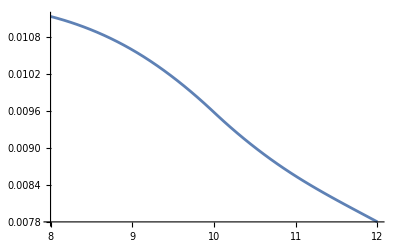

```mathematica
Plot[Im@solXmmbarMode3["Solution"][4][r],{r,8,12}]
```

## Triangular system

```mathematica
odeCoeffFuns=<|
"Xmmbar"->Function[{z0},LHSCoeffXmmb[bg,z0]],"Xnm"->Function[{z0},LHSCoeffXnm[bg,z0]],
"Xnn"->Function[{z0},LHSCoeffXnn[bg,z0]]|>;
```

```mathematica
corrData=loadCorrectorData[mtest,bulkDir,bdyDir];

stressSources=<||>;
```

```mathematica
modePars=<|"omegaMK"->3,"ethBuilder"->makeHeldEthModeBuilder[bg],"ethBarBuilder"->makeHeldEthBarModeBuilder[bg],"sTll"->0,"sTlm"->1,"sTlmb"->-1|>;
```

```mathematica
profiles=makeBoundaryProfiles[corrData];
```

```mathematica
ops=makeBoundaryDerivativeProfiles[profiles,mtest,modePars["omegaMK"],modePars["ethBuilder"],modePars["ethBarBuilder"],modePars["sTll"],modePars["sTlm"],modePars["sTlmb"]];

ops["ethTllDeltaPrime"][0.2]
ops["ethTlmbDeltaPrime"][0.2]
ops["ethbarTlmDeltaPrime"][0.2]
```

-0.0188717+0.0273843 ⅈ

0.0165122+0.0025378 ⅈ

0.03594+0.0182687 ⅈ

### X_(m m̄)

```mathematica
bgFunXmmbar=MakeBoundaryBGFun[bg,First[tinyGridData["Xmmbar"]["RGrid"]]];

initXmmbar=makeInitDataXmmbar[corrData,bgFunXmmbar];
sourceFieldXmmbar=makeSourceFieldXmmbar[mtest,bg,tinyGridData["Xmmbar"]["RGrid"],tinyGridData["Xmmbar"]["ZGrid"],0,"Reduced"];
```

```mathematica
solXmmbar=ZSliceSolveSecondOrder[sourceFieldXmmbar,odeCoeffFuns["Xmmbar"],initXmmbar];
```

```mathematica
solXmmbar[[1]]
```

InterpolatingFunction[…]

## X_nm

```mathematica
packBuilders=<|"Xmmbar"->Function[{sol,m,bg,rGrid,zGrid},buildXmmbarPack[sol,m,bg,modePars["omegaMK"],rGrid,zGrid]],"Xnm"->Function[{sol,m,bg,rGrid,zGrid},buildXnmPack[sol,m,bg,modePars["omegaMK"],rGrid,zGrid]]|>;
```

```mathematica
rGridXnm=tinyGridData["Xnm"]["RGrid"];
zGridXnm=tinyGridData["Xnm"]["ZGrid"];
```

```mathematica
gmmbarPack=buildXmmbarPack[solXmmbar,mtest,bg,modePars["omegaMK"],rGridXnm,zGridXnm];

sourceFieldXnm=makeSourceFieldXnm[gmmbarPack,bg,rGridXnm,zGridXnm,Lookup[stressSources,"Tlm",0],"Reduced"];
```

```mathematica
bgFunXnm=MakeBoundaryBGFun[bg,First[tinyGridData["Xnm"]["RGrid"]]];
```

```mathematica
initXnm=makeInitDataXnm[corrData,bgFunXnm,ops["ethTllDeltaPrime"]];
```

```mathematica
solXnm=ZSliceSolveSecondOrder[sourceFieldXnm,odeCoeffFuns["Xnm"],initXnm];
```

```mathematica
solXnm[[1]]
```

InterpolatingFunction[…]

```mathematica
iz=2;
z0=zGrid[[iz]]
```

-0.81

```mathematica
ClearAll[smokeTestXnmSlice];

smokeTestXnmSlice[iz_Integer]:=Module[{z0,s,a0,a1,a2,y0,yp0,rmin,rmax,rr,u,eq,sol,rtest,resVals,srcVals,relRes},z0=zGrid[[iz]];
s=SliceInterpolant[sourceFieldXnm,iz];
{a0,a1,a2}=odeCoeffFuns["Xnm"][z0];
{y0,yp0}=initXnm[z0];
rmin=First[rGrid];
rmax=Last[rGrid];
If[!And@@(NumericQ/@{y0,yp0})||!FreeQ[{y0,yp0},DirectedInfinity|ComplexInfinity|Indeterminate],Return[<|"iz"->iz,"z0"->z0,"Status"->"Bad initial data","IC"->{y0,yp0}|>]];
If[!And@@Table[NumericQ[a0[r]]&&NumericQ[a1[r]]&&NumericQ[a2[r]]&&NumericQ[s[r]],{r,{rmin,(rmin+rmax)/2,rmax}}],Return[<|"iz"->iz,"z0"->z0,"Status"->"Non-numeric coeff/source"|>]];
eq=u''[rr]==(s[rr]-a1[rr] u'[rr]-a0[rr] u[rr])/a2[rr];
sol=Quiet@Check[NDSolveValue[{eq,u[rmin]==y0,u'[rmin]==yp0},u,{rr,rmin,rmax}],$Failed];
If[sol===$Failed,Return[<|"iz"->iz,"z0"->z0,"Status"->"Solve failed"|>]];
rtest=Subdivide[rmin,rmax,50];
resVals=Quiet@Abs[(a2[#] sol''[#]+a1[#] sol'[#]+a0[#] sol[#]-s[#])&/@rtest];
srcVals=Quiet@Abs[s/@rtest];
relRes=Max[resVals]/Max[Join[srcVals,{10.^-30}]];
<|"iz"->iz,"z0"->z0,"Status"->"OK","y0"->y0,"yp0"->yp0,"MaxAbsResidual"->Max[resVals],"MaxRelResidual"->relRes,"Solution"->sol|>];
```

```mathematica
testMid=smokeTestXnmSlice[9]
```

<|iz→9,z0→-0.18,Status→OK,y0→-0.0143475-0.0093997 ⅈ,yp0→-0.0667541+0.0255331 ⅈ,MaxAbsResidual→0.0000130733,MaxRelResidual→0.0134443,Solution→InterpolatingFunction[…]|>

```mathematica
s=SliceInterpolant[sourceFieldXnm,iz];
{a0,a1,a2}=odeCoeffFuns["Xnm"][z0];
{y0,yp0}=initXnm[z0];

testPts=N@{First[rGrid],Mean[{First[rGrid],Last[rGrid]}],Last[rGrid]};

<|"z0"->z0,"Heads"->(Head/@{s,a0,a1,a2,y0,yp0}),"InitNumericQ"->(NumericQ/@{y0,yp0}),"CoeffNumericQAtPts"->Table[rr->(NumericQ/@{a0[rr],a1[rr],a2[rr],s[rr]}),{rr,testPts}],"CoeffValuesAtPts"->Table[rr->N@{a0[rr],a1[rr],a2[rr],s[rr]},{rr,testPts}]|>
```

<|z0→-0.81,Heads→{InterpolatingFunction,Function,Function,Function,Complex,Complex},InitNumericQ→{True,True},CoeffNumericQAtPts→{8.→{True,True,True,True},10.→{True,True,True,True},12.→{True,True,True,True}},CoeffValuesAtPts→{8.→{-0.015625,0.125+0. ⅈ,0.5,-0.000655214-0.000044946 ⅈ},10.→{-0.01,0.1+0. ⅈ,0.5,-0.000361501-0.0000247979 ⅈ},12.→{-0.00694444,0.0833333+0. ⅈ,0.5,-0.000208007-0.0000142685 ⅈ}}|>

```mathematica
Table[{zz,initXnm[zz]},{zz,{-0.9,-0.99,-0.999,-0.9999}}]
```

{{-0.9,{-0.000323882-0.000185525 ⅈ,7.06005×10^-7-0.00024474 ⅈ}},{-0.99,{-0.0000150097-3.68661×10^-6 ⅈ,-0.000154341+0.000186371 ⅈ}},{-0.999,{-1.50096×10^-6-3.68657×10^-7 ⅈ,-0.0000457732+0.0000626616 ⅈ}},{-0.9999,{-1.50082×10^-7-3.68624×10^-8 ⅈ,-0.000014172+0.0000201889 ⅈ}}}

## X_nn

## Smoke-test for X_(m m̄)

```mathematica
(* ::Section::*)(*x_mmbar manufactured-solution checks*)ClearAll[XmmbLHSExpr,MakeManufacturedXmmbProblem,ReconstructSliceField,XmmbResidualField,XmmbErrorField,XmmbSliceErrorReport,XmmbMaxError,XmmbMaxResidual];

(*radial operator acting on an expression expr[r,z]*)
XmmbLHSExpr[expr_,bg_Association]:=Module[{a=bg["a"],Σ},Σ=r^2+a^2 z^2;
D[expr,{r,2}]+(2 r/Σ) D[expr,r]+(4 a^2 z^2/Σ^2) expr];

ReconstructSliceField[solAssoc_Association,rGrid_List,zGrid_List]:=MakeGridField[Table[solAssoc[iz][rGrid[[ir]]],{ir,Length[rGrid]},{iz,Length[zGrid]}],rGrid,zGrid];

(*build source+exact boundary data from an exact solution*)
MakeManufacturedXmmbProblem[exactExpr_,bg_Association,rGrid_List,zGrid_List]:=Module[{sourceExpr,sourceField,rmin},rmin=First[rGrid];
sourceExpr=XmmbLHSExpr[exactExpr,bg];
sourceField=SampleExprOnGrid[sourceExpr,rGrid,zGrid];
<|"ExactExpr"->exactExpr,"SourceExpr"->sourceExpr,"SourceField"->sourceField,"InitDataFun"->Function[z0,N@{exactExpr/. {r->rmin,z->z0},D[exactExpr,r]/. {r->rmin,z->z0}}]|>];

XmmbErrorField[solAssoc_Association,exactExpr_,rGrid_List,zGrid_List]:=MakeGridField[Table[solAssoc[iz][rGrid[[ir]]]-N[exactExpr/. {r->rGrid[[ir]],z->zGrid[[iz]]}],{ir,Length[rGrid]},{iz,Length[zGrid]}],rGrid,zGrid];

XmmbResidualField[solAssoc_Association,sourceField_Association,bg_Association]:=Module[{rGrid,zGrid,vals,s,a0,a1,a2},rGrid=sourceField["Meta"]["RGrid"];
zGrid=sourceField["Meta"]["ZGrid"];
vals=Table[s=SliceInterpolant[sourceField,iz];
{a0,a1,a2}=LHSCoeffXmmb[bg,zGrid[[iz]]];
a2[rGrid[[ir]]] solAssoc[iz]''[rGrid[[ir]]]+a1[rGrid[[ir]]] solAssoc[iz]'[rGrid[[ir]]]+a0[rGrid[[ir]]] solAssoc[iz][rGrid[[ir]]]-s[rGrid[[ir]]],{ir,Length[rGrid]},{iz,Length[zGrid]}];
MakeGridField[vals,rGrid,zGrid]];

XmmbSliceErrorReport[errField_Association]:=Module[{rGrid,zGrid,vals},rGrid=errField["Meta"]["RGrid"];
zGrid=errField["Meta"]["ZGrid"];
vals=errField["Data"];
Table[<|"iz"->iz,"z"->zGrid[[iz]],"MaxAbsErrorOnSlice"->Max[Abs[vals[[All,iz]]]]|>,{iz,Length[zGrid]}]];

XmmbMaxError[errField_Association]:=Max[Abs[errField["Data"]]];
XmmbMaxResidual[resField_Association]:=Max[Abs[resField["Data"]]];
```

```mathematica
ClearAll[ExactXmmbTest,XmmbLHSExpr];

ExactXmmbTest[r_,z_]:=Exp[-(r-7)^2/6] (1+z+2 z^2);

XmmbLHSExpr[expr_,bg_Association]:=Module[{a=bg["a"],Σ},Σ=r^2+a^2 z^2;
D[expr,{r,2}]+(2 r/Σ) D[expr,r]+(4 a^2 z^2/Σ^2) expr];
```

```mathematica
sourceExpr=XmmbLHSExpr[ExactXmmbTest[r,z],bg];
sourceField=SampleExprOnGrid[sourceExpr,rGrid,zGrid];

initDataFun=Function[z0,N@{ExactXmmbTest[First[rGrid],z0],D[ExactXmmbTest[r,z],r]/. {r->First[rGrid],z->z0}}];
```

```mathematica
solXmmb=ZSliceSolveSecondOrder[sourceField,Function[z0,LHSCoeffXmmb[bg,z0]],initDataFun];
```

NDSolveValue::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

```mathematica
errField=MakeGridField[Table[solXmmb[iz][rGrid[[ir]]]-ExactXmmbTest[rGrid[[ir]],zGrid[[iz]]],{ir,Length[rGrid]},{iz,Length[zGrid]}],rGrid,zGrid];

Max[Abs[errField["Data"]]]
```

0.00361633

## Tests

```mathematica
bg=MakeBackground[<|"M"->1.0,"a"->0.7,"Q"->0.0|>];

gmmbar=MakeReducedField[Exp[-(r-7)^2] (1+z^2),0,{0.3,2}];
gnm=MakeReducedField[Exp[-(r-8)^2] (1-z+z^2),1,{0.3,2}];

gmmbarPack=BuildReducedHeldDerivPack[gmmbar,bg];
gnmPack=BuildReducedHeldDerivPack[gnm,bg];

sxnmRed=SourceXnmReducedExpr[gmmbarPack,bg,0,"Raw"];
sxnnRed=SourceXnnReducedExpr[gmmbarPack,gnmPack,bg,0,"Raw"];

NumericValueAt[sxnmRed,10.,0.99]
NumericValueAt[sxnnRed,10.,0.99]
```

-0.000187248-0.000015716 ⅈ

-0.541912

## Test Helpers

```mathematica
(* ::Section::*)(*Test helpers*)ClearAll[ExprZeroQ,ExprEqualQ,SamplePointsRZ,NumericGridMax,SmoothG0,SmoothG1,SmoothGm1,MakeRawField,RawFieldExpr,RawFieldSpin,RawFieldMode,MakeRawFieldFromReduced];

ExprZeroQ[expr_,asm_:$Assumptions]:=TrueQ@Assuming[asm,FullSimplify[expr==0]];

ExprEqualQ[a_,b_,asm_:$Assumptions]:=ExprZeroQ[a-b,asm];

SamplePointsRZ[rmin_,rmax_,nr_,zmin_,zmax_,nz_]:=Flatten[Table[{rr,zz},{rr,Subdivide[rmin,rmax,nr-1]},{zz,Subdivide[zmin,zmax,nz-1]}],1];

NumericGridMax[expr_,pts_List]:=Max@Abs@(NumericValueAt[expr,#[[1]],#[[2]]]&/@pts);

SmoothG0[r_,z_]:=Exp[-(r-7)^2/5] (1+z+2 z^2);
SmoothG1[r_,z_]:=Exp[-(r-8)^2/7] (1-z+z^2);
SmoothGm1[r_,z_]:=Exp[-(r-6)^2/4] (1+3 z+z^2);

MakeRawField[expr_,s_Integer,{ω_,m_Integer}]:=<|"Expr"->expr,"Spin"->s,"Mode"-><|"ω"->ω,"m"->m|>|>;

RawFieldExpr[f_Association]:=f["Expr"];
RawFieldSpin[f_Association]:=f["Spin"];
RawFieldMode[f_Association]:=f["Mode"];

MakeRawFieldFromReduced[red_Association]:=MakeRawField[RawExpr[red],RedSpin[red],{ModeOmega[red],ModeM[red]}];
```

### Raw derivative pack for cross-checks

```mathematica
ClearAll[HeldPRawField,HeldPpRawField,HeldEthRawField,HeldEthBarRawField,BuildRawDerivPackFromRaw];

HeldPRawField[field_Association,bg_Association]:=MakeRawField[D[RawFieldExpr[field],r],RawFieldSpin[field],{RawFieldMode[field]["ω"],RawFieldMode[field]["m"]}];

HeldPpRawField[field_Association,bg_Association]:=Module[{ω,expr},ω=RawFieldMode[field]["ω"];
expr=RawFieldExpr[field];
MakeRawField[-I ω expr-(DeltaBG[bg,r]/(2 SigmaBG[bg,r,z])) D[expr,r],RawFieldSpin[field],{RawFieldMode[field]["ω"],RawFieldMode[field]["m"]}]];

HeldEthRawField[field_Association,bg_Association]:=Module[{mm,ss,ω,expr,λ},mm=RawFieldMode[field]["m"];
ss=RawFieldSpin[field];
ω=RawFieldMode[field]["ω"];
expr=RawFieldExpr[field];
λ=Sqrt[1-z^2];
MakeRawField[(1/Sqrt[2]) (λ D[expr,z]-bg["a"] ω λ expr+((mm+ss z)/λ) expr),ss+1,{ω,mm}]];

HeldEthBarRawField[field_Association,bg_Association]:=Module[{mm,ss,ω,expr,λ},mm=RawFieldMode[field]["m"];
ss=RawFieldSpin[field];
ω=RawFieldMode[field]["ω"];
expr=RawFieldExpr[field];
λ=Sqrt[1-z^2];
MakeRawField[(1/Sqrt[2]) (λ D[expr,z]+bg["a"] ω λ expr-((mm+ss z)/λ) expr),ss-1,{ω,mm}]];

BuildRawDerivPackFromRaw[field_Association,bg_Association]:=<|"X"->field,"P_X"->HeldPRawField[field,bg],"Pp_X"->HeldPpRawField[field,bg],"EH_X"->HeldEthRawField[field,bg],"EbH_X"->HeldEthBarRawField[field,bg],"EH_P_X"->HeldEthRawField[HeldPRawField[field,bg],bg],"EbH_P_X"->HeldEthBarRawField[HeldPRawField[field,bg],bg],"EbH_EH_X"->HeldEthBarRawField[HeldEthRawField[field,bg],bg],"PpHr_P_X"->HeldPpRawField[HeldPRawField[field,bg],bg]|>;
```

## Operator consistency tests

```mathematica
ClearAll[OperatorConsistencyTests];

OperatorConsistencyTests[m0_Integer,s0_Integer,bg_Association,ω0_:0.3]:=Module[{g,raw,tests},g=MakeReducedField[G[r,z],s0,{ω0,m0}];
raw=MakeRawFieldFromReduced[g];
tests={VerificationTest[ExprEqualQ[RawExpr[HeldPRedField[g,bg]],RawFieldExpr[HeldPRawField[raw,bg]]],True,TestID->"thorn consistency"],VerificationTest[ExprEqualQ[RawExpr[HeldPpRedField[g,bg]],RawFieldExpr[HeldPpRawField[raw,bg]]],True,TestID->"thornPrime consistency"],VerificationTest[ExprEqualQ[RawExpr[HeldEthRedField[g,bg]],RawFieldExpr[HeldEthRawField[raw,bg]]],True,TestID->"eth consistency"],VerificationTest[ExprEqualQ[RawExpr[HeldEthBarRedField[g,bg]],RawFieldExpr[HeldEthBarRawField[raw,bg]]],True,TestID->"ethbar consistency"]};
TestReport[tests]];

(* ::Section::*)(*Numeric operator consistency diagnostics/tests*)ClearAll[SmoothGTest,OperatorConsistencyDiagnostics,OperatorConsistencyTests];

(* smooth G test-function *)
SmoothGTest[r_,z_]:=Exp[-(r-7)^2/5] (1+z+2 z^2+z^3);

OperatorConsistencyDiagnostics[m0_Integer,s0_Integer,bg_Association,ω0_:0.3,fun_:SmoothGTest]:=Module[{g,raw,pts,dP,dPp,dE,dEb,vP,vPp,vE,vEb},g=MakeReducedField[fun[r,z],s0,{ω0,m0}];
raw=MakeRawFieldFromReduced[g];
dP=Together[RawExpr[HeldPRedField[g,bg]]-RawFieldExpr[HeldPRawField[raw,bg]]];
dPp=Together[RawExpr[HeldPpRedField[g,bg]]-RawFieldExpr[HeldPpRawField[raw,bg]]];
dE=Together[RawExpr[HeldEthRedField[g,bg]]-RawFieldExpr[HeldEthRawField[raw,bg]]];
dEb=Together[RawExpr[HeldEthBarRedField[g,bg]]-RawFieldExpr[HeldEthBarRawField[raw,bg]]];
pts=SamplePointsRZ[2.5,12.0,6,-0.95,0.95,7];
vP=NumericValueAt[dP,#[[1]],#[[2]]]&/@pts;
vPp=NumericValueAt[dPp,#[[1]],#[[2]]]&/@pts;
vE=NumericValueAt[dE,#[[1]],#[[2]]]&/@pts;
vEb=NumericValueAt[dEb,#[[1]],#[[2]]]&/@pts;
<|"Points"->pts,"thornDiffExpr"->dP,"thornPrimeDiffExpr"->dPp,"ethDiffExpr"->dE,"ethbarDiffExpr"->dEb,"thornValues"->vP,"thornPrimeValues"->vPp,"ethValues"->vE,"ethbarValues"->vEb,"thornMaxAbs"->Max[Abs[vP]],"thornPrimeMaxAbs"->Max[Abs[vPp]],"ethMaxAbs"->Max[Abs[vE]],"ethbarMaxAbs"->Max[Abs[vEb]]|>];

OperatorConsistencyTests[m0_Integer,s0_Integer,bg_Association,ω0_:0.3,fun_:SmoothGTest,tol_:10^-10]:=Module[{diag},diag=OperatorConsistencyDiagnostics[m0,s0,bg,ω0,fun];
TestReport[{VerificationTest[NumericQ[diag["thornMaxAbs"]]&&diag["thornMaxAbs"]<tol,True,TestID->"thorn consistency"],VerificationTest[NumericQ[diag["thornPrimeMaxAbs"]]&&diag["thornPrimeMaxAbs"]<tol,True,TestID->"thornPrime consistency"],VerificationTest[NumericQ[diag["ethMaxAbs"]]&&diag["ethMaxAbs"]<tol,True,TestID->"eth consistency"],VerificationTest[NumericQ[diag["ethbarMaxAbs"]]&&diag["ethbarMaxAbs"]<tol,True,TestID->"ethbar consistency"]}]];
```

```mathematica
OperatorConsistencyTests[2,0,bg]
OperatorConsistencyTests[2,1,bg]
```

TestReportObject[…]

TestReportObject[…]

```mathematica
bg=MakeBackground[<|"M"->1.0,"a"->0.7,"Q"->0.0|>];

diagOp=OperatorConsistencyDiagnostics[2,1,bg];
diagOp["thornMaxAbs"]
diagOp["thornPrimeMaxAbs"]
diagOp["ethMaxAbs"]
diagOp["ethbarMaxAbs"]

OperatorConsistencyTests[2,1,bg]
```

0.

4.33934×10^-16

6.17606×10^-13

7.26595×10^-13

TestReportObject[…]

## Source consistency tests

```mathematica
(* ::Section::*)(*Source consistency tests*)
(* ::Section::*)(*Numeric source consistency diagnostics/tests*)ClearAll[SmoothTll,SmoothTlm,SmoothTln,SourceConsistencyDiagnostics,SourceConsistencyTests];

SmoothTll[r_,z_]:=Exp[-(r-6)^2/6] (1+z^2);
SmoothTlm[r_,z_]:=Exp[-(r-8)^2/7] (1-z+z^2);
SmoothTln[r_,z_]:=Exp[-(r-9)^2/8] (1+2 z^2);

SourceConsistencyDiagnostics[m0_Integer,bg_Association,ω0_:0.3]:=Module[{gmmbar,gnm,gmmbarPack,gnmPack,sxmmbRed,sxnmRed,sxnnRed,sxmmbRaw,sxnmRaw,sxnnRaw,d0,d1,d2,pts,v0,v1,v2},gmmbar=MakeReducedField[SmoothG0[r,z],0,{ω0,m0}];
gnm=MakeReducedField[SmoothG1[r,z],1,{ω0,m0}];
gmmbarPack=BuildReducedHeldDerivPack[gmmbar,bg];
gnmPack=BuildReducedHeldDerivPack[gnm,bg];
sxmmbRed=SourceXmmbReducedExpr[m0,SmoothTll[r,z],"Raw"];
sxnmRed=SourceXnmReducedExpr[gmmbarPack,bg,SmoothTlm[r,z],"Raw"];
sxnnRed=SourceXnnReducedExpr[gmmbarPack,gnmPack,bg,SmoothTln[r,z],"Raw"];
sxmmbRaw=SmoothTll[r,z];
sxnmRaw=NofXmmbRawExpr[gmmbarPack,bg]+SmoothTlm[r,z];
sxnnRaw=Re[SmoothTln[r,z]]+Re[UofXmmbRawExpr[gmmbarPack,bg]]+Re[VofXnmRawExpr[gnmPack,bg]];
d0=Together[TargetWeight[m0,0] sxmmbRed-sxmmbRaw];
d1=Together[TargetWeight[m0,1] sxnmRed-sxnmRaw];
d2=Together[TargetWeight[m0,0] sxnnRed-sxnnRaw];
pts=SamplePointsRZ[2.5,12.0,6,-0.95,0.95,7];
v0=NumericValueAt[d0,#[[1]],#[[2]]]&/@pts;
v1=NumericValueAt[d1,#[[1]],#[[2]]]&/@pts;
v2=NumericValueAt[d2,#[[1]],#[[2]]]&/@pts;
<|"xmmbDiffExpr"->d0,"xnmDiffExpr"->d1,"xnnDiffExpr"->d2,"xmmbMaxAbs"->Max[Abs[v0]],"xnmMaxAbs"->Max[Abs[v1]],"xnnMaxAbs"->Max[Abs[v2]]|>];

SourceConsistencyTests[m0_Integer,bg_Association,ω0_:0.3,tol_:10^-9]:=Module[{diag},diag=SourceConsistencyDiagnostics[m0,bg,ω0];
TestReport[{VerificationTest[NumericQ[diag["xmmbMaxAbs"]]&&diag["xmmbMaxAbs"]<tol,True,TestID->"xmmb reduced/raw consistency"],VerificationTest[NumericQ[diag["xnmMaxAbs"]]&&diag["xnmMaxAbs"]<tol,True,TestID->"xnm reduced/raw consistency"],VerificationTest[NumericQ[diag["xnnMaxAbs"]]&&diag["xnnMaxAbs"]<tol,True,TestID->"xnn reduced/raw consistency"]}]];
```

```mathematica
diagSrc=SourceConsistencyDiagnostics[2,bg];
diagSrc["xmmbMaxAbs"]
diagSrc["xnmMaxAbs"]
diagSrc["xnnMaxAbs"]

SourceConsistencyTests[2,bg]
```

0.

1.06014×10^-14

0.

TestReportObject[…]

## Regularity tests

```mathematica
(* Regularity diagnostics and tests: check numerical regularity tests near the poles*)
ClearAll[RegularityTests];

(**)
ClearAll[NumericGridValues,RegularityDiagnostics,RegularityTests];
NumericGridValues[expr_,pts_List]:=NumericValueAt[expr,#[[1]],#[[2]]]&/@pts;

RegularityDiagnostics[m0_Integer,bg_Association,ω0_:0.3]:=Module[{gmmbar,gnm,gmmbarPack,gnmPack,sxnmRed,sxnnRed,ptsNearPoles,vals1,vals2,bad1,bad2},

gmmbar=MakeReducedField[SmoothG0[r,z],0,{ω0,m0}];
gnm=MakeReducedField[SmoothG1[r,z],1,{ω0,m0}];

gmmbarPack=BuildReducedHeldDerivPack[gmmbar,bg];
gnmPack=BuildReducedHeldDerivPack[gnm,bg];

sxnmRed=SourceXnmReducedExpr[gmmbarPack,bg,0,"Raw"];
sxnnRed=SourceXnnReducedExpr[gmmbarPack,gnmPack,bg,0,"Raw"];

ptsNearPoles=Join[SamplePointsRZ[2.2,15.0,7,-0.999,-0.9,6],SamplePointsRZ[2.2,15.0,7,0.9,0.999,6]];
vals1=NumericGridValues[sxnmRed,ptsNearPoles];
vals2=NumericGridValues[sxnnRed,ptsNearPoles];
bad1=Pick[Transpose[{ptsNearPoles,vals1}],Not/@(NumericQ/@vals1)];
bad2=Pick[Transpose[{ptsNearPoles,vals2}],Not/@(NumericQ/@vals2)];

<|"Points"->ptsNearPoles,"sxnmValues"->vals1,"sxnnValues"->vals2,"sxnmBadValues"->bad1,"sxnnBadValues"->bad2,"sxnmMaxAbs"->If[bad1==={},Max[Abs[vals1]],Missing["NonNumeric"]],"sxnnMaxAbs"->If[bad2==={},Max[Abs[vals2]],Missing["NonNumeric"]]|>];

RegularityTests[m0_Integer,bg_Association,ω0_:0.3]:=Module[{diag},
diag=RegularityDiagnostics[m0,bg,ω0];

TestReport[{
VerificationTest[diag["sxnmBadValues"]==={},True,
TestID->"xnm reduced source numeric near poles"],VerificationTest[diag["sxnnBadValues"]==={},True,TestID->"xnn reduced source numeric near poles"]}]];
```

```mathematica
Table[{zz,NumericValueAt[sxnmRed,10.,zz],NumericValueAt[sxnnRed,10.,zz]},{zz,{-0.999,-0.99,-0.9,0.9,0.99,0.999}}]
```

{{-0.999,-0.000104055-7.0484×10^-6 ⅈ,-5.44027},{-0.99,-0.000102557-7.01231×10^-6 ⅈ,-0.490894},{-0.9,-0.0000885979-6.69487×10^-6 ⅈ,-0.00163156},{0.9,-0.0001671-0.000014509 ⅈ,-0.0483289},{0.99,-0.000187248-0.000015716 ⅈ,-0.541912},{0.999,-0.000189341-0.0000158424 ⅈ,-5.49172}}

```mathematica
Table[{zz,NumericValueAt[(1-z^2) sxnnRed,10.,zz]},{zz,{-0.999,-0.99,-0.9,0.9,0.99,0.999}}]
```

{{-0.999,-0.0108751},{-0.99,-0.00976879},{-0.9,-0.000309997},{0.9,-0.00918249},{0.99,-0.0107841},{0.999,-0.010978}}

```mathematica
Table[{zz,NumericValueAt[Sqrt[1-z^2] sxnnRed,10.,zz]},{zz,{-0.999,-0.99,-0.9,0.9,0.99,0.999}}]
```

{{-0.999,-0.243236},{-0.99,-0.0692491},{-0.9,-0.000711182},{0.9,-0.0210661},{0.99,-0.0764462},{0.999,-0.245536}}

```mathematica
diag=RegularityDiagnostics[2,bg];
diag["sxnmMaxAbs"]
diag["sxnnMaxAbs"]

RegularityTests[2,bg]
```

0.361383

121.509

TestReportObject[…]

## Smoke Tests

```mathematica
(* ::Section::*)(*Hierarchy smoke test*)ClearAll[ReconstructSliceField,HierarchySmokeTest];

ReconstructSliceField[solAssoc_Association,rGrid_List,zGrid_List]:=MakeGridField[Table[solAssoc[iz][rGrid[[ir]]],{ir,Length[rGrid]},{iz,Length[zGrid]}],rGrid,zGrid];

HierarchySmokeTest[m0_Integer,bg_Association,ω0_:0.3,rGrid_:N@Subdivide[2.2,15.0,60],zGrid_:N@Subdivide[-0.98,0.98,24]]:=Module[{gmmbar,gnm,gmmbarPack,gnmPack,sxmmbRed,sxnmRed,sxnnRed,sxmmbField,sxnmField,sxnnField,solXmmb,solXnm,solXnn,xmmbarField,xnmField,xnnField},gmmbar=MakeReducedField[SmoothG0[r,z],0,{ω0,m0}];
gnm=MakeReducedField[SmoothG1[r,z],1,{ω0,m0}];
gmmbarPack=BuildReducedHeldDerivPack[gmmbar,bg];
gnmPack=BuildReducedHeldDerivPack[gnm,bg];
sxmmbRed=SourceXmmbReducedExpr[m0,SmoothTll[r,z],"Raw"];
sxnmRed=SourceXnmReducedExpr[gmmbarPack,bg,SmoothTlm[r,z],"Raw"];
sxnnRed=SourceXnnReducedExpr[gmmbarPack,gnmPack,bg,SmoothTln[r,z],"Raw"];
sxmmbField=SampleExprOnGrid[sxmmbRed,rGrid,zGrid];
sxnmField=SampleExprOnGrid[sxnmRed,rGrid,zGrid];
sxnnField=SampleExprOnGrid[sxnnRed,rGrid,zGrid];
solXmmb=ZSliceSolveSecondOrder[sxmmbField,Function[z0,LHSCoeffXmmb[bg,z0]],Function[z0,{0.0,0.0}]];
solXnm=ZSliceSolveSecondOrder[sxnmField,Function[z0,LHSCoeffXnm[bg,z0]],Function[z0,{0.0,0.0}]];
solXnn=ZSliceSolveFirstOrder[sxnnField,Function[z0,LHSCoeffXnn[bg,z0]],Function[z0,0.0]];
xmmbarField=ReconstructSliceField[solXmmb,rGrid,zGrid];
xnmField=ReconstructSliceField[solXnm,rGrid,zGrid];
xnnField=ReconstructSliceField[solXnn,rGrid,zGrid];
<|"SourceXmmb"->sxmmbField,"SourceXnm"->sxnmField,"SourceXnn"->sxnnField,"SolXmmb"->solXmmb,"SolXnm"->solXnm,"SolXnn"->solXnn,"FieldXmmb"->xmmbarField,"FieldXnm"->xnmField,"FieldXnn"->xnnField|>];
```

```mathematica
bg=MakeBackground[<|"M"->1.0,"a"->0.7,"Q"->0.0|>];

smoke=HierarchySmokeTest[2,bg];
Keys[smoke]
```

{SourceXmmb,SourceXnm,SourceXnn,SolXmmb,SolXnm,SolXnn,FieldXmmb,FieldXnm,FieldXnn}

```mathematica
smoke["SolXmmb"][1][10.0]
smoke["SolXnm"][10][10.0]
smoke["SolXnn"][20][10.0]
```

450.5

15.7847+0.407997 ⅈ

-84.7136

### Smoke Show Reults

```mathematica
ClearAll[FieldDensityPlot];

FieldDensityPlot[field_Association,part_:Re,label_:""]:=Module[{rGrid,zGrid,data},rGrid=field["Meta"]["RGrid"];
zGrid=field["Meta"]["ZGrid"];
data=Flatten[Table[{rGrid[[ir]],zGrid[[iz]],part[field["Data"][[ir,iz]]]},{ir,Length[rGrid]},{iz,Length[zGrid]}],1];
ListDensityPlot[data,InterpolationOrder->2,Frame->True,FrameLabel->{"r","z"},PlotLabel->label,PlotLegends->Automatic]];
```

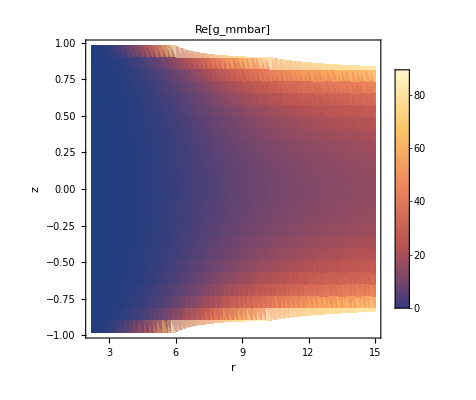

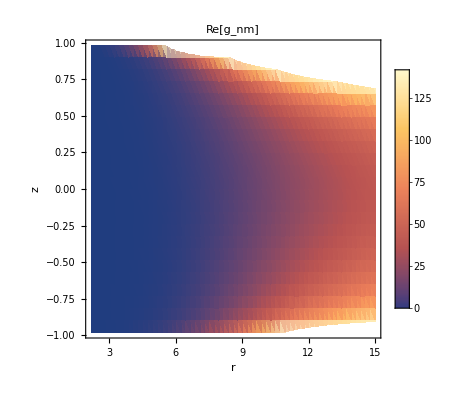

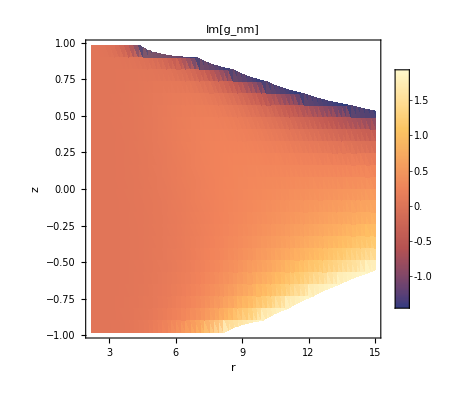

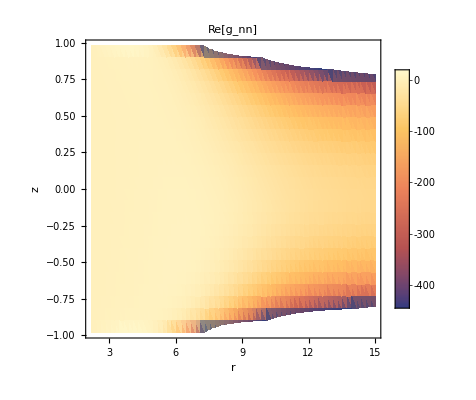

```mathematica
FieldDensityPlot[smoke["FieldXmmb"],Re,"Re[g_mmbar]"]
FieldDensityPlot[smoke["FieldXnm"],Re,"Re[g_nm]"]
FieldDensityPlot[smoke["FieldXnm"],Im,"Im[g_nm]"]
FieldDensityPlot[smoke["FieldXnn"],Re,"Re[g_nn]"]
```